## V27: I want to verify that the substitution ϕ -> ϕ/χt works at the microscopic level

```mathematica
Quit[]
```

```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

```mathematica
InitializationValue[$Initialization] = Hold[$HistoryLength = 2];
<<"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\Kay-initialization.m"
"Directory for read/write is \"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\MathematicaFiles-LRW-DLA-bLRW\\LaplaceEqSolver&MORE\\\""
Quiet[<<"D:\Offline_Documents\University\PhD_Paris\PhD_work\Simulations\MathematicaFiles-LRW-DLA-bLRW\LRW-initialization.m"]
```

Directory for read/write is "D:\Offline_Documents\University\PhD_Paris\PhD_work\Simulations\MathematicaFiles-LRW-DLA-bLRW\LaplaceEqSolver&MORE\"

Directory for read/write is "D:\Offline_Documents\University\PhD_Paris\PhD_work\Simulations\MathematicaFiles-LRW-DLA-bLRW\LaplaceEqSolver&MORE\"

# Final Dynamical theories

## FinalDynamicLERWaction[] BENCHMARK

This action should be:

For fields that do not have a color index, we default to set it to j_-1, because in the WickContraction[] it automated with color indices.
Instead, the source is set with index 1, so that it can contract with an external “probe”

```mathematica
Clear[FinalDynamicLERWaction];
Options[FinalDynamicLERWaction]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"startingTime"->1,"endTime"->10};

FinalDynamicLERWaction[OptionsPattern[]]:=Module[{locGraph,locStartingTime,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,γ];


locGraph=OptionValue["graph"];
locStartingTime =OptionValue["startingTime"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[
If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,
(*FALSE*)V[(1+γ Sum[locWeights[[x,y]](R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, y]]ψs[x,Subscript[t, T+1],Subscript[ll, x]]-ϕs[x,Subscript[t, T+1],Subscript[k, x]])χs[y,Subscript[t, T],1]*ϕ[x,Subscript[t, T],Subscript[k, x]],{y,Length[locVertices]}]+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}]
+(*COPY ϕ*) ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]]
+(*COPY ψ*) ψs[x,Subscript[t, T+1],Subscript[ll, x]]*ψ[x,Subscript[t, T],Subscript[ll, x]]) ]
],{x,Length[locVertices]}]
V[(1+ ϕs[locSource,Subscript[t, T+1],Subscript[k, locSource]]ϕ[locSource,Subscript[t, T],Subscript[k, locSource]]+χ[locSource,Subscript[t, T],1])];

action=Product[actionTimeSlice[T],{T,locEndTime}];

Return[action]

]
```

### Usage example of DynamicLERWaction[]

My favorite graph

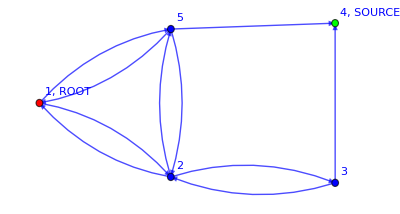

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

```mathematica
fields=FieldsNamesGenerator[{ϕ,χ,ψ}];
g=myFavoriteGraph;
endTime=1;
Z=FinalDynamicLERWaction["graph"->g,"endTime"->endTime]/.β[__]->1;
Z0=Z/.γ->0;
```

Observable ϕs[1,t_1,k_1]

```mathematica
ϕs[1,Subscript[t, 1],Subscript[k, 1]]/Znorm[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"βrule"->{β[__]->1}];

expLERWbenchmark =ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand;
```

```mathematica
Replace[expLERWbenchmark,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"βrule"->{β[__]->1}]),1];

expLERWbenchmark2=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_2"//Expand;
```

```mathematica
Replace[expLERWbenchmark2,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"βrule"->{β[__]->1}]),1];

expLERWbenchmark3=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_3"//Expand;
```

### ConvergenceLERW[] NO NORMALIZATION BY HAND

I want to check whether I really get the wrong result if I do not normalize at each step

```mathematica
Clear[ConvergenceLERW];
Options[ConvergenceLERW]={"graph"->g,"fields"->FieldsNamesGenerator[{ϕ,ψ,χ}],"steps"->10,"precision"->10^-9,"gammaValue"->0.1};

ConvergenceLERW[operator_,OptionsPattern[]]:=Module[{Z,locOperator,locPrecision,locγ,exp,i,temp,token},

i=1;

Z=FinalDynamicLERWaction["graph"->OptionValue[ "graph"],"endTime"->1]/.β[__]->1.;

locOperator= operator ;
locPrecision=OptionValue["precision"];
locγ=OptionValue["gammaValue"];

exp=ExpectationValueBlock[Z locOperator,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1},"graph"->OptionValue[ "graph"],"nχ"->(-1)];
exp=exp/.Subscript[t, a_]->Subscript[t, a-1];
exp=exp/.γ->locγ;

(*Print["########## i="<>ToString[i]<>", "<>ToString[(Coefficient[exp, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0)]<>" ############"];*)

For[i=2,i<=OptionValue["steps"] && (Coefficient[exp,  ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0/.γ->locγ)>=locPrecision,i++,

exp=ExpectationValueBlock[Z exp,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1},"graph"->OptionValue[ "graph"],"nχ"->(-1)];
exp=exp/.Subscript[t, a_]->Subscript[t, a-1];
exp=exp/.γ->locγ;

];


Print["########## i=",i,", ",(Coefficient[exp, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0)," ############"];

Return[exp];
]
```

#### Test ConvergenceLERW[]

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
g=myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]];
```

```mathematica
g=myFavoriteGraph;
precision=10^-15;
expLERW=ConvergenceLERW[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"steps"->100,"precision"->precision,"gammaValue"->0.3]
```

########## i=57, 9.20358×10^-16 ############

0.+9.20358×10^-16 ϕs[1,t_1,k_1]+3.97867×10^-8 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+7.29385×10^-15 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]+1.16077×10^-7 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]+7.73847×10^-8 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]+0.108434 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[3,t_1,ll_3]+5.66125×10^-6 R[1,5,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]+0.0000104152 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]+5.66085×10^-6 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[5,t_1,ll_5]+0.0722891 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[5,t_1,ll_5]+0.0232245 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[3,t_1,ll_3] ψs[5,t_1,ll_5]

```mathematica
expLERW1/.ϕs[__]->1/.ψs[__]->1/.R[__]->1
```

expLERW1

```mathematica
expLERW1/.a_/;Abs[a]<10^-6:>0/.ϕs[__]->1/.ψs[__]->1
```

expLERW1

```mathematica
(*THIS DOES NOT WORK: THE PROBABILITY IS NOT CONSERVED!!!*)
```

## LRWactionχDenominator[]

I am using the formalism in which ϕ -> ϕ/χ̃ 
The 1/χ̃ must always be understood in terms of its expansion. Since I only have ONE TARGET, I should be able to truncate its expansion just to first order. 
However, we cannot expand around χ̃=0 directly. I use the expansion around χ̃=1 and then keep the first order in χ̃.
									
To reach the final result I’ll go slowly and check how the action behave by adding contributions one by one

### Expansion of the microscopic action

b=1

```mathematica
Sum[ Exp[-λ n],{n,0,∞},Assumptions->λ>0];
order1=Series[%,{λ,0,7}]
Sum[ n Exp[-λ n],{n,0,∞},Assumptions->λ>0];
orderχ=Series[%,{λ,0,7}]
```

1/λ+1/2+λ/12-λ^3/720+λ^5/30240-λ^7/1209600+O[λ]^8

1/λ^2-1/12+λ^2/240-λ^4/6048+λ^6/172800+O[λ]^8

```mathematica
(* So, const is 1/2 *)
```

If I factor out the order(1) before extracting finite part:

```mathematica
orderχ/order1
```

1/λ-1/2+λ/12-λ^3/720+λ^5/30240-λ^7/1209600+O[λ]^8

```mathematica
orderχ/(order1)^2
```

1-λ+λ^2/2-λ^3/6+λ^4/24-λ^5/120+λ^6/720-λ^7/5040+λ^8/40320+O[λ]^9

Subbed in the action

```mathematica
Zsubϕ*ⅇ^(-ϕ[1,Subscript[t, 1],Subscript[k, 1]] ϕs[1,Subscript[t, 1],Subscript[k, 1]])/( χs[1,Subscript[t, 1],1,1])/.V[a_]->a;
%/.ϕ[a___,Subscript[k, b_]]:>ϕ[a,Subscript[k, b]]/( χs[a,1,1]);
%//. 1/χs[a__]^n_.:> (const + κ χs[a]/12)^n;
Normal@Series[%,{κ,0,1}]/.ϕ[a__]->ϕ[a]/const//FullSimplify;
Collect[%,(ⅇ^(ψ[1,Subscript[t, 1],Subscript[ll, 1]] ψs[1,Subscript[t, 2],Subscript[ll, 1]])+Σβ R[1,2,RGBColor[0, 0, 1]] χ[1,Subscript[t, 1],Subscript[i, 1],Subscript[α, 1]] χs[2,Subscript[t, 1],Subscript[i, 1],Subscript[α, 1]]+γ Σβ ϕ[1,Subscript[t, 1],Subscript[k, 1]] χs[2,Subscript[t, 1],1,1] (-ϕs[1,Subscript[t, 2],Subscript[k, 1]]+R[1,2,RGBColor[1, 0, 0]] ϕs[2,Subscript[t, 2],Subscript[k, 2]] ψs[1,Subscript[t, 2],Subscript[ll, 1]]))];
%/.(ⅇ^(ψ[1,Subscript[t, 1],Subscript[ll, 1]] ψs[1,Subscript[t, 2],Subscript[ll, 1]])+Σβ R[1,2,RGBColor[0, 0, 1]] χ[1,Subscript[t, 1],Subscript[i, 1],Subscript[α, 1]] χs[2,Subscript[t, 1],Subscript[i, 1],Subscript[α, 1]]+γ Σβ ϕ[1,Subscript[t, 1],Subscript[k, 1]] χs[2,Subscript[t, 1],1,1] (-ϕs[1,Subscript[t, 2],Subscript[k, 1]]+R[1,2,RGBColor[1, 0, 0]] ϕs[2,Subscript[t, 2],Subscript[k, 2]] ψs[1,Subscript[t, 2],Subscript[ll, 1]]))-> ⅇ^(-S)/.(-ⅇ^(ψ[1,Subscript[t, 1],Subscript[ll, 1]] ψs[1,Subscript[t, 2],Subscript[ll, 1]])-Σβ R[1,2,RGBColor[0, 0, 1]] χ[1,Subscript[t, 1],Subscript[i, 1],Subscript[α, 1]] χs[2,Subscript[t, 1],Subscript[i, 1],Subscript[α, 1]]+γ Σβ ϕ[1,Subscript[t, 1],Subscript[k, 1]] χs[2,Subscript[t, 1],1,1] (ϕs[1,Subscript[t, 2],Subscript[k, 1]]-R[1,2,RGBColor[1, 0, 0]] ϕs[2,Subscript[t, 2],Subscript[k, 2]] ψs[1,Subscript[t, 2],Subscript[ll, 1]]))-> -ⅇ^(-S);
Collect[%//Expand,ⅇ^(-S+ϕ[1,Subscript[t, 1],Subscript[k, 1]] (-ϕs[1,Subscript[t, 1],Subscript[k, 1]]+ϕs[1,Subscript[t, 2],Subscript[k, 1]])),FullSimplify];
%/.χs[a__]χs[b__]->0
```

ⅇ^(-S+ϕ[1,t_1,k_1] (-ϕs[1,t_1,k_1]+ϕs[1,t_2,k_1])) (const+1/12 κ (1+ϕ[1,t_1,k_1] (-ϕs[1,t_1,k_1]+ϕs[1,t_2,k_1])) χs[1,t_1,1,1])

b>1 WHAT FOLLOWS IS WRONG! I CANNOT USE THE SIMPLIFICATION \boldχ=(χ)^b IN THE MICROSCOPIC!!

(χ̃)^b

```mathematica
Series[x^b,{x,1,6}]//FullSimplify
```

1+b (x-1)+1/2 (-1+b) b (x-1)^2+1/6 (-2+b) (-1+b) b (x-1)^3+1/24 (-3+b) (-2+b) (-1+b) b (x-1)^4+1/120 (-4+b) (-3+b) (-2+b) (-1+b) b (x-1)^5+1/720 (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) b (x-1)^6+O[x-1]^7

```mathematica
Sum[Binomial[b,n](x-1)^n,{n,0,∞}]
```

x^b

```mathematica
Sum[Binomial[b,n](-1)^n,{n,0,∞}]
Sum[Binomial[b,n]n(-1)^n,{n,1,∞}]
```

HypergeometricPFQ[{-b},{},1]

-b HypergeometricPFQ[{1-b},{},1]

```mathematica
-b HypergeometricPFQ[{1-b},{},1]/.b->5
```

0

This function is  ZERO for all b > 1. (expected)

1/(χ̃)^b

```mathematica
Sum[Binomial[-b,n](x-1)^n,{n,0,∞}]
```

x^-b

```mathematica
Sum[Binomial[-b,n](-1)^n,{n,0,∞}]
Sum[Binomial[-b,n]n(-1)^n,{n,1,∞}]
```

HypergeometricPFQ[{b},{},1]

b HypergeometricPFQ[{1+b},{},1]

```mathematica
(* This function is divergent for all b∈Reals, We want to regularize it *)
```

This function is divergent for all b ∈ Reals. We want to regularize it with ⅇ^λ.
One should expand the result of the sum up to O[λ]^b so that the divergence is compensated. The generating functionals are
											1:     
											χ̃: 
If one wants to factorize the first, then the “weight” is just given by . NOT TRUE!!!
The problem is that now there is no closed form for the dependence on b!

```mathematica
bValue=1;
Limit[D[(1-ⅇ^-λ)^-b λ^b,{λ,bValue}]/bValue!,λ->0]/.b->bValue
Limit[D[b ⅇ^(b λ) (-1+ⅇ^λ)^(-1-b) λ^b-b/λ,{λ,bValue}]/bValue!,λ->0]/.b->bValue
Limit[D[b  (-1+ⅇ^λ)^-1 ,λ],λ->0];
```

1/2

-1/12

If I factor out the contribution of ∑1:

```mathematica
Sum[Binomial[-b,n](-1)^n n Exp[-λ n],{n,1,∞},Assumptions->λ>0]//FullSimplify
Series[%,{λ,0,4}]//FullSimplify
%/.b->1
%/(1/λ+1/2)
```

b ⅇ^(b λ) (-1+ⅇ^λ)^(-1-b)

λ^-b (b/λ+1/2 (-1+b) b+1/24 (-2+b) b (-1+3 b) λ+1/48 (-3+b) (-1+b) b^2 λ^2+((-4+b) b (2+5 b (1+3 (-2+b) b)) λ^3)/5760+((-5+b) (-1+b) b^2 (-2+b (-7+3 b)) λ^4)/11520+O[λ]^5)

1/λ^2-1/12+λ^2/240+O[λ]^4

1/λ-1/2+λ/6-λ^2/12+(11 λ^3)/240-(11 λ^4)/480+O[λ]^5

```mathematica
Sum[Binomial[-b,n](-1)^n Exp[-λ n],{n,0,∞},Assumptions->λ>0]
Series[%,{λ,0,4}]//FullSimplify
%/.b->1
```

(1-ⅇ^-λ)^-b

λ^-b (1+(b λ)/2+1/24 b (-1+3 b) λ^2+1/48 (-1+b) b^2 λ^3+(b (2+5 b (1+3 (-2+b) b)) λ^4)/5760+O[λ]^5)

1/λ+1/2+λ/12-λ^3/720+O[λ]^4

computations to get the generating functions

```mathematica
Sum[Binomial[-b,n](-1)^n Exp[-λ n],{n,0,∞},Assumptions->λ>0]* λ^b
Series[%,{λ,0,4}]
```

(1-ⅇ^-λ)^-b λ^b

1+(b λ)/2+1/24 (-b+3 b^2) λ^2+1/48 (-b^2+b^3) λ^3+((2 b+5 b^2-30 b^3+15 b^4) λ^4)/5760+O[λ]^5

```mathematica
Sum[Binomial[-b,n](-1)^n n Exp[-λ n],{n,1,∞},Assumptions->λ>0]* λ^b-b/λ//FullSimplify
Series[%,{λ,0,4}]//FullSimplify
%/.b->2;
```

b (-1/λ+ⅇ^(b λ) (-1+ⅇ^λ)^(-1-b) λ^b)

1/2 (-1+b) b+1/24 (-2+b) b (-1+3 b) λ+1/48 (-3+b) (-1+b) b^2 λ^2+((-4+b) b (2+5 b (1+3 (-2+b) b)) λ^3)/5760+((-5+b) (-1+b) b^2 (-2+b (-7+3 b)) λ^4)/11520+O[λ]^5

```mathematica
((λ ⅇ^λ)/(-1+ⅇ^λ) )^b b/(-1+ⅇ^λ) 
Series[%,{λ,0,4}]//FullSimplify;
%//TeXForm;
```

(b ((ⅇ^λ λ)/(-1+ⅇ^λ))^b)/(-1+ⅇ^λ)

Sub in the action

```mathematica
Zsubϕ= V[ⅇ^(ϕ[1,Subscript[t, 1],Subscript[k, 1]] ϕs[1,Subscript[t, 2],Subscript[k, 1]])] V[ⅇ^(ψ[1,Subscript[t, 1],Subscript[ll, 1]] ψs[1,Subscript[t, 2],Subscript[ll, 1]])+γ ϕ[1,Subscript[t, 1],Subscript[k, 1]] (Σβ χs[2,Subscript[t, 1],1] (-ϕs[1,Subscript[t, 2],Subscript[k, 1]]+R[1,2,RGBColor[1,0,0]] ϕs[2,Subscript[t, 2],Subscript[k, 2]] ψs[1,Subscript[t, 2],Subscript[ll, 1]]))+χ[1,Subscript[t, 1],Subscript[i, 1]] (R[1,2,RGBColor[0,0,1]] Σβ χs[2,Subscript[t, 1],Subscript[i, 1]])] /.{
χs[a___,1]:>χs[a,1,1],
χ[a___,Subscript[i, b_]]:>χ[a,Subscript[i, b],Subscript[α, b]],
χs[a___,Subscript[i, b_]]:>χs[a,Subscript[i, b],Subscript[α, b]],
β[__]->1}//Simplify(* ATTENTION: β is set to 1*)
```

V[ⅇ^(ϕ[1,t_1,k_1] ϕs[1,t_2,k_1])] V[ⅇ^(ψ[1,t_1,ll_1] ψs[1,t_2,ll_1])+Σβ R[1,2,RGBColor[0, 0, 1]] χ[1,t_1,i_1,α_1] χs[2,t_1,i_1,α_1]+γ Σβ ϕ[1,t_1,k_1] χs[2,t_1,1,1] (-ϕs[1,t_2,k_1]+R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_2,k_2] ψs[1,t_2,ll_1])]

```mathematica
Zsubϕ*ⅇ^(-ϕ[1,Subscript[t, 1],Subscript[k, 1]] ϕs[1,Subscript[t, 1],Subscript[k, 1]])/( χs[1,Subscript[t, 1],1,1])/.V[a_]->a;
%/.ϕ[a___,Subscript[k, b_]]:>ϕ[a,Subscript[k, b]]/( χs[a,1,1]);
%//. 1/χs[a__]^n_.:> (const + κ χs[a]/12)^n;
Normal@Series[%,{κ,0,1}]/.ϕ[a__]->ϕ[a]/const//FullSimplify;
Collect[%,(ⅇ^(ψ[1,Subscript[t, 1],Subscript[ll, 1]] ψs[1,Subscript[t, 2],Subscript[ll, 1]])+Σβ R[1,2,RGBColor[0, 0, 1]] χ[1,Subscript[t, 1],Subscript[i, 1],Subscript[α, 1]] χs[2,Subscript[t, 1],Subscript[i, 1],Subscript[α, 1]]+γ Σβ ϕ[1,Subscript[t, 1],Subscript[k, 1]] χs[2,Subscript[t, 1],1,1] (-ϕs[1,Subscript[t, 2],Subscript[k, 1]]+R[1,2,RGBColor[1, 0, 0]] ϕs[2,Subscript[t, 2],Subscript[k, 2]] ψs[1,Subscript[t, 2],Subscript[ll, 1]]))];
%/.(ⅇ^(ψ[1,Subscript[t, 1],Subscript[ll, 1]] ψs[1,Subscript[t, 2],Subscript[ll, 1]])+Σβ R[1,2,RGBColor[0, 0, 1]] χ[1,Subscript[t, 1],Subscript[i, 1],Subscript[α, 1]] χs[2,Subscript[t, 1],Subscript[i, 1],Subscript[α, 1]]+γ Σβ ϕ[1,Subscript[t, 1],Subscript[k, 1]] χs[2,Subscript[t, 1],1,1] (-ϕs[1,Subscript[t, 2],Subscript[k, 1]]+R[1,2,RGBColor[1, 0, 0]] ϕs[2,Subscript[t, 2],Subscript[k, 2]] ψs[1,Subscript[t, 2],Subscript[ll, 1]]))-> ⅇ^(-S)/.(-ⅇ^(ψ[1,Subscript[t, 1],Subscript[ll, 1]] ψs[1,Subscript[t, 2],Subscript[ll, 1]])-Σβ R[1,2,RGBColor[0, 0, 1]] χ[1,Subscript[t, 1],Subscript[i, 1],Subscript[α, 1]] χs[2,Subscript[t, 1],Subscript[i, 1],Subscript[α, 1]]+γ Σβ ϕ[1,Subscript[t, 1],Subscript[k, 1]] χs[2,Subscript[t, 1],1,1] (ϕs[1,Subscript[t, 2],Subscript[k, 1]]-R[1,2,RGBColor[1, 0, 0]] ϕs[2,Subscript[t, 2],Subscript[k, 2]] ψs[1,Subscript[t, 2],Subscript[ll, 1]]))-> -ⅇ^(-S);
Collect[%//Expand,ⅇ^(-S+ϕ[1,Subscript[t, 1],Subscript[k, 1]] (-ϕs[1,Subscript[t, 1],Subscript[k, 1]]+ϕs[1,Subscript[t, 2],Subscript[k, 1]])),FullSimplify]
%/.χs[a__]χs[b__]->0
```

ⅇ^(-S+ϕ[1,t_1,k_1] (-ϕs[1,t_1,k_1]+ϕs[1,t_2,k_1])) (const+1/12 κ (1+ϕ[1,t_1,k_1] (-ϕs[1,t_1,k_1]+ϕs[1,t_2,k_1])) χs[1,t_1,1,1])-1/12 ⅇ^(ϕ[1,t_1,k_1] (-ϕs[1,t_1,k_1]+ϕs[1,t_2,k_1])) γ κ Σβ ϕ[1,t_1,k_1] χs[1,t_1,1,1] χs[2,t_1,1,1] (ϕs[1,t_2,k_1]-R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_2,k_2] ψs[1,t_2,ll_1])

ⅇ^(-S+ϕ[1,t_1,k_1] (-ϕs[1,t_1,k_1]+ϕs[1,t_2,k_1])) (const+1/12 κ (1+ϕ[1,t_1,k_1] (-ϕs[1,t_1,k_1]+ϕs[1,t_2,k_1])) χs[1,t_1,1,1])

### LRWactionχDenominatorContributionFromMeasure[] (just the denominator from dϕ)

```mathematica
Clear[LRWactionχDenominatorContributionFromMeasure];
Options[LRWactionχDenominatorContributionFromMeasure]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"startingTime"->1,"endTime"->10};

LRWactionχDenominatorContributionFromMeasure[OptionsPattern[]]:=Module[{locGraph,locStartingTime,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,γ];


locGraph=OptionValue["graph"];
locStartingTime =OptionValue["startingTime"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[
If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,
(*FALSE*)V[(1+γ Sum[locWeights[[x,y]](R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, y]]ψs[x,Subscript[t, T+1],Subscript[ll, x]]-ϕs[x,Subscript[t, T+1],Subscript[k, x]])χs[y,Subscript[t, T],1]*ϕ[x,Subscript[t, T],Subscript[k, x]],{y,Length[locVertices]}]+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}]
+(*COPY ϕ*) ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]]
+(*COPY ψ*) ψs[x,Subscript[t, T+1],Subscript[ll, x]]*ψ[x,Subscript[t, T],Subscript[ll, x]]) ]*
(* CONTRIBUTION FROM THE MEASURE *)
V[(1+ 1/12 χs[x,Subscript[t, T],1])]
],{x,Length[locVertices]}]
If[ MemberQ[OptionValue["excludedVertices"],locSource],1,
V[(1+ ϕs[locSource,Subscript[t, T+1],Subscript[k, locSource]]ϕ[locSource,Subscript[t, T],Subscript[k, locSource]]+χ[locSource,Subscript[t, T],1])]
];

action=Product[actionTimeSlice[T],{T,locEndTime}];

Return[action]

]
```

#### Usage example of LRWactionχDenominatorContributionFromMeasure[]

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
fields=FieldsNamesGenerator[{ϕ,ψ,χ}];
g=myFavoriteGraph;
endTime=1;
Z=LRWactionχDenominatorContributionFromMeasure["graph"->g,"endTime"->endTime]/.β[__]->1;
Z0=Z/.γ->0;
```

```mathematica
ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"theory"->LRWactionχDenominatorContributionFromMeasure]
```

11/27

Observable ϕs[1,t_1,k_1]

Step 1

```mathematica
ϕs[1,Subscript[t, 1],Subscript[k, 1]]/ZnormGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"βrule"->{β[__]->1},"theory"->LRWactionχDenominatorContributionFromMeasure];
(*ϕs[1,Subscript[t, 1],Subscript[k, 1]];*)

expLRWχDenominatorContributionFromMeasure =ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1;
```

ϕs[1,t_1,k_1]-3/4 γ_1 ϕs[1,t_1,k_1]+15/44 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+9/22 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]

```mathematica
expLERWbenchmark
```

ϕs[1,t_1,k_1]-11/13 γ_1 ϕs[1,t_1,k_1]+5/13 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+6/13 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]

```mathematica
15./44
5./13
```

0.340909

0.384615

Step 2

```mathematica
Replace[expLRWχDenominatorContributionFromMeasure,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"theory"->LRWactionχDenominatorContributionFromMeasure]),1];

expLRWχDenominatorContributionFromMeasure2=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_2"//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1

```mathematica
Replace[expLRWχDenominatorContributionFromMeasure2,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"theory"->LRWactionχDenominatorContributionFromMeasure]),1];

expLRWχDenominatorContributionFromMeasure3=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_3"//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1

```mathematica
Replace[expLRWχDenominatorContributionFromMeasure3,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"theory"->LRWactionχDenominatorContributionFromMeasure]),1];

expLRWχDenominatorContributionFromMeasure4=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_4"//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1

```mathematica
(* SEEMS TO WORK, LET US CHECK THE CONVERGENCE *)
```

#### Convergence

```mathematica
(* SEEMS TO WORK, LET US CHECK THE CONVERGENCE *)
(* It actually works! This means that the measure does not affect the result, as anticipated *)
```

```mathematica
g=myFavoriteGraph;
precision=10^-10;

expLRWχDenominatorContributionFromMeasureCONV=ConvergenceGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"theory"->LRWactionχDenominatorContributionFromMeasure,
"fields"->FieldsNamesGenerator[{ϕ,ψ,χ}],"graph"->g,"steps"->100,"precision"->precision,"gammaValue"->0.3];
```

########## i=100, 8.51472×10^-12 ############

```mathematica
expLRWχDenominatorContributionFromMeasureCONV/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1.

```mathematica
expLRWχDenominatorContributionFromMeasureCONV/.a_/;Abs[a]<10^-6:>0/.ϕs[__]->1/.ψs[__]->1
Rationalize[%,0.0001]
```

0.272727 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+0.0909089 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+0.454545 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+0.181818 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]

3/11 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+1/11 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+5/11 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+2/11 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]

GRAND TOTAL CHECK

```mathematica
(expLRWχDenominatorContributionFromMeasureCONV/.ϕs[__]->1/.ψs[__]->1)-
(3/11 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+
1/11 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+
5/11 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+
2/11 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]);
(*%/.a_/;(Abs[a]<precision):>0*)
If[(%/.R[__]->1)<precision, Print["\t!!!!! IT WORKS !!!!!!"];(%/.R[__]->1), Print["\txxxxxxxx NOOOOOO xxxxxxxx"];(%/.R[__]->1)]
```

!!!!! IT WORKS !!!!!!

-1.04763×10^-15

Speed test VS benchmark

```mathematica
g=myFavoriteGraph;
precision=10^-5;

ConvergenceGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"theory"->LRWactionχDenominatorContributionFromMeasure,
"fields"->FieldsNamesGenerator[{ϕ,ψ,χ}],"graph"->g,"steps"->100,"precision"->precision,"gammaValue"->0.3];

ConvergenceGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"theory"->LRWaction,
"fields"->FieldsNamesGenerator[{ϕ,ψ,χ}],"graph"->g,"steps"->100,"precision"->precision,"gammaValue"->0.3];

%%-%
```

########## i=46, 8.08869×10^-6 ############

########## i=40, 8.1872×10^-6 ############

0.-9.85054×10^-8 ϕs[1,t_1,k_1]-0.0000176334 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]-1.83837×10^-6 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]-0.0000482115 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]-0.000030302 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]+0.0000588184 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[3,t_1,ll_3]-0.00022737 R[1,5,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]+1.57675×10^-6 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]-0.000247382 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[5,t_1,ll_5]+0.0000373733 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[5,t_1,ll_5]+0.000475066 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[3,t_1,ll_3] ψs[5,t_1,ll_5]

```mathematica
g=myFavoriteGraph;
precision=10^-7;

ConvergenceGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"theory"->LRWactionχDenominatorContributionFromMeasure,
"fields"->FieldsNamesGenerator[{ϕ,ψ,χ}],"graph"->g,"steps"->100,"precision"->precision,"gammaValue"->0.3];

ConvergenceGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"theory"->LRWaction,
"fields"->FieldsNamesGenerator[{ϕ,ψ,χ}],"graph"->g,"steps"->100,"precision"->precision,"gammaValue"->0.3];
```

########## i=64, 8.22828×10^-8 ############

########## i=56, 7.5577×10^-8 ############

### LRWactionχDenominatorContributionFromMeasureExtended[] I CAN TRUNCATE!

Let us see if I can effectively truncate:
YES!!!

```mathematica
Clear[LRWactionχDenominatorContributionFromMeasureExtended];
Options[LRWactionχDenominatorContributionFromMeasureExtended]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"startingTime"->1,"endTime"->10};

LRWactionχDenominatorContributionFromMeasureExtended[OptionsPattern[]]:=Module[{locGraph,locStartingTime,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,γ];


locGraph=OptionValue["graph"];
locStartingTime =OptionValue["startingTime"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[
If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,
(*FALSE*)V[(1+γ Sum[locWeights[[x,y]](R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, y]]ψs[x,Subscript[t, T+1],Subscript[ll, x]]-ϕs[x,Subscript[t, T+1],Subscript[k, x]])χs[y,Subscript[t, T],1]*ϕ[x,Subscript[t, T],Subscript[k, x]],{y,Length[locVertices]}]+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}]
+(*COPY ϕ*) ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]]
+(*COPY ψ*) ψs[x,Subscript[t, T+1],Subscript[ll, x]]*ψ[x,Subscript[t, T],Subscript[ll, x]]) ]*
(* CONTRIBUTION FROM THE MEASURE *)
V[(1+ 1/12 χs[x,Subscript[t, T],1]+χs[x,Subscript[t, T],1]χs[x,Subscript[t, T],1])]
],{x,Length[locVertices]}]
If[ MemberQ[OptionValue["excludedVertices"],locSource],1,
V[(1+ ϕs[locSource,Subscript[t, T+1],Subscript[k, locSource]]ϕ[locSource,Subscript[t, T],Subscript[k, locSource]]+χ[locSource,Subscript[t, T],1])]
];

action=Product[actionTimeSlice[T],{T,locEndTime}];

Return[action]

]
```

#### Usage example of LRWactionχDenominatorContributionFromMeasureExtended[]

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
fields=FieldsNamesGenerator[{ϕ,ψ,χ}];
g=myFavoriteGraph;
endTime=1;
Z=LRWactionχDenominatorContributionFromMeasureExtended["graph"->g,"endTime"->endTime]/.β[__]->1;
Z0=Z/.γ->0;
```

Observable ϕs[1,t_1,k_1]

Step 1

```mathematica
ϕs[1,Subscript[t, 1],Subscript[k, 1]]/ZnormGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"βrule"->{β[__]->1},"theory"->LRWactionχDenominatorContributionFromMeasureExtended,"MAXnumberOfDer"->3];
(*ϕs[1,Subscript[t, 1],Subscript[k, 1]];*)

expLRWχDenominatorContributionFromMeasure =ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->3]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

ϕs[1,t_1,k_1]-3/4 γ_1 ϕs[1,t_1,k_1]+15/44 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+9/22 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]

1

Step 2

```mathematica
Replace[expLRWχDenominatorContributionFromMeasure,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"theory"->LRWactionχDenominatorContributionFromMeasureExtended]),1];

expLRWχDenominatorContributionFromMeasure2=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_2"//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1

```mathematica
Replace[expLRWχDenominatorContributionFromMeasure2,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"theory"->LRWactionχDenominatorContributionFromMeasureExtended]),1];

expLRWχDenominatorContributionFromMeasure3=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_3"//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1

```mathematica
Replace[expLRWχDenominatorContributionFromMeasure3,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"theory"->LRWactionχDenominatorContributionFromMeasureExtended]),1];

expLRWχDenominatorContributionFromMeasure4=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_4"//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1

```mathematica
(* SEEMS TO WORK, LET US CHECK THE CONVERGENCE *)
```

### LRWactionχDenominatorContributionFromGaussianTruncated[] IT WORKS

Now I guess I can expand the Exp too:

```mathematica
Series[Exp[a x],{x,0,2}]
```

1+a x+(a^2 x^2)/2+O[x]^3

Check that I can truncate the exponential: YES

```mathematica
theory=LRWactionχDenominatorContributionFromMeasure;

Z=theory["graph"->g,"endTime"->endTime]/.β[__]->1;

ExpectationValueBlock[Z V[Exp[-ϕs[1,Subscript[t, 1],Subscript[k, 1]]*ϕ[1,Subscript[t, 1],Subscript[k, 1]](1+ a χs[1,Subscript[t, 1],1]-1)]],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->2]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand

ExpectationValueBlock[Z V[1-ϕs[1,Subscript[t, 1],Subscript[k, 1]]*ϕ[1,Subscript[t, 1],Subscript[k, 1]](1+ a χs[1,Subscript[t, 1],1]-1)],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->2]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand
```

11/27-(11 a)/36

11/27-(11 a)/36

```mathematica
Clear[LRWactionχDenominatorContributionFromGaussianTruncated];
Options[LRWactionχDenominatorContributionFromGaussianTruncated]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"startingTime"->1,"endTime"->10};

LRWactionχDenominatorContributionFromGaussianTruncated[OptionsPattern[]]:=Module[{locGraph,locStartingTime,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,γ];


locGraph=OptionValue["graph"];
locStartingTime =OptionValue["startingTime"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[
If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,
(*FALSE*)V[(1+γ Sum[locWeights[[x,y]](R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, y]]ψs[x,Subscript[t, T+1],Subscript[ll, x]]-ϕs[x,Subscript[t, T+1],Subscript[k, x]])χs[y,Subscript[t, T],1]*ϕ[x,Subscript[t, T],Subscript[k, x]],{y,Length[locVertices]}]+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}]
+(*COPY ϕ*) ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]]
+(*COPY ψ*) ψs[x,Subscript[t, T+1],Subscript[ll, x]]*ψ[x,Subscript[t, T],Subscript[ll, x]]) ]*
(* CONTRIBUTION FROM THE MEASURE *)
V[(1+ 1/12 χs[x,Subscript[t, T],1])]*
(* CONTRIBUTION FROM GAUSSIAN TERM TRUNCATED *)
(*V[Exp[-ϕs[x,Subscript[t, T],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]](1+ 1/12 χs[x,Subscript[t, T],1]-1)]]*)V[1-ϕs[x,Subscript[t, T],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]](1+1/12 χs[x,Subscript[t, T],1]-1)]
],{x,Length[locVertices]}]
If[ MemberQ[OptionValue["excludedVertices"],locSource],1,
V[(1+ ϕs[locSource,Subscript[t, T+1],Subscript[k, locSource]]ϕ[locSource,Subscript[t, T],Subscript[k, locSource]]+χ[locSource,Subscript[t, T],1])]
(* CONTRIBUTION FROM GAUSSIAN TERM *)
(*V[Exp[-ϕs[locSource,Subscript[t, T],Subscript[k, locSource]]*ϕ[locSource,Subscript[t, T],Subscript[k, locSource]](1+ 1/12 χs[locSource,Subscript[t, T],1]-1)]]*)
(*V[1-ϕs[locSource,Subscript[t, T],Subscript[k, locSource]]*ϕ[locSource,Subscript[t, T],Subscript[k, locSource]](1+ 1/12 χs[locSource,Subscript[t, T],1]-1)]*)
];

action=Product[actionTimeSlice[T],{T,locEndTime}];

Return[action]

]
```

#### test for modified WickContraction

```mathematica
ExpectationValueBlock[V[(b ϕs[1,Subscript[t, 1],Subscript[k, 1]]ϕ[1,Subscript[t, 1],Subscript[k, 1]])^3]a,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]
```

6 a b^3

```mathematica
ExpectationValueBlock[a*V[ⅇ^(b ϕs[1,Subscript[t, 1],Subscript[k, 1]]ϕ[1,Subscript[t, 1],Subscript[k, 1]])],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->6]
```

a+a b+a b^2+a b^3+a b^4+a b^5+a b^6

```mathematica
ExpectationValueBlock[V[Exp[-ϕs[1,Subscript[t, 1],Subscript[k, 1]]*ϕ[1,Subscript[t, 1],Subscript[k, 1]](1+ 1/12 χs[1,Subscript[t, 1],1]-1)]](Exp[χ[1,Subscript[t, 1],1]]),"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->False,"graph"->g]
```

1-1/12 δ[1,1]+1/144 δ[1,1]^2-δ[1,1]^3/1728+δ[1,1]^4/20736

```mathematica
WickContractionBlock[V[1-ϕs[1,Subscript[t, 1],Subscript[k, 1]]*ϕ[1,Subscript[t, 1],Subscript[k, 1]](1+ 1/12 χs[1,Subscript[t, 1],1]-1)]χ[1,Subscript[t, 1],1],"fields"->FieldsNamesGenerator[{ϕ,χ}]]
```

-1/12 δ[1,1]

#### Usage example of LRWactionχDenominatorContributionFromGaussianTruncated[]

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
fields=FieldsNamesGenerator[{ϕ,ψ,χ}];
g=myFavoriteGraph;
endTime=1;
theory=LRWactionχDenominatorContributionFromGaussianTruncated;

Z=theory["graph"->g,"endTime"->endTime]/.β[__]->1;
Z0=Z/.γ->0;
```

Observable ϕs[1,t_1,k_1]

Check which field order is faster: best seems to be {ϕ, ψ, χ}

```mathematica
AbsoluteTiming[ExpectationValueBlock[Z ϕs[1,Subscript[t, 1],Subscript[k, 1]],"endTime"->endTime,"fields"->FieldsNamesGenerator[{ϕ,ψ,χ}],"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand]
```

{43.8068,13/18 ϕs[1,t_1,k_1]-11/18 γ_1 ϕs[1,t_1,k_1]+5/18 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+1/3 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]}

```mathematica
AbsoluteTiming[ExpectationValueBlock[Z ϕs[1,Subscript[t, 1],Subscript[k, 1]],"endTime"->endTime,"fields"->FieldsNamesGenerator[{ψ,χ,ϕ}],"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand]
```

{59.727,13/18 ϕs[1,t_1,k_1]-11/18 γ_1 ϕs[1,t_1,k_1]+5/18 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+1/3 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]}

```mathematica
AbsoluteTiming[ExpectationValueBlock[Z ϕs[1,Subscript[t, 1],Subscript[k, 1]],"endTime"->endTime,"fields"->FieldsNamesGenerator[{χ,ψ,ϕ}],"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand]
```

{58.4185,13/18 ϕs[1,t_1,k_1]-11/18 γ_1 ϕs[1,t_1,k_1]+5/18 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+1/3 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]}

```mathematica
AbsoluteTiming[ExpectationValueBlock[Z ϕs[1,Subscript[t, 1],Subscript[k, 1]],"endTime"->endTime,"fields"->FieldsNamesGenerator[{χ,ϕ,ψ}],"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand]
```

{58.3048,13/18 ϕs[1,t_1,k_1]-11/18 γ_1 ϕs[1,t_1,k_1]+5/18 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+1/3 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]}

Step 1

```mathematica
ϕs[1,Subscript[t, 1],Subscript[k, 1]]/ZnormGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"βrule"->{β[__]->1},"theory"->theory,"MAXnumberOfDer"->1];
(*ϕs[1,Subscript[t, 1],Subscript[k, 1]];*)

expLRWχDenominatorContributionFromGaussian =ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1;
```

ϕs[1,t_1,k_1]-11/13 γ_1 ϕs[1,t_1,k_1]+5/13 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+6/13 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]

```mathematica
expLRWχDenominatorContributionFromGaussian/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1

Step 2

```mathematica
Replace[expLRWχDenominatorContributionFromGaussian,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"theory"->theory,"MAXnumberOfDer"->1]),1];

expLRWχDenominatorContributionFromGaussian2=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_2"//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1

Step 3 etc

```mathematica
Replace[expLRWχDenominatorContributionFromMeasure2,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"theory"->theory]),1];

expLRWχDenominatorContributionFromMeasure3=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_3"//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1

```mathematica
Replace[expLRWχDenominatorContributionFromMeasure3,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"theory"->theory]),1];

expLRWχDenominatorContributionFromMeasure4=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_4"//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1

```mathematica
(* SEEMS TO WORK, LET US CHECK THE CONVERGENCE *)
```

#### Convergence

```mathematica
(* SEEMS TO WORK, LET US CHECK THE CONVERGENCE *)
(* It actually works! This means that the measure does not affect the result, as anticipated *)
```

```mathematica
g=myFavoriteGraph;
precision=10^-10;

expLRWχDenominatorContributionFromGaussianCONV=ConvergenceGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"theory"->theory,
"fields"->FieldsNamesGenerator[{ϕ,ψ,χ}],"graph"->g,"steps"->200,"precision"->precision,"gammaValue"->0.4,"MAXnumberOfDer"->1];
```

########## i=200, 1.29128×10^-36 ############

```mathematica
expLRWχDenominatorContributionFromGaussianCONV/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1.

```mathematica
expLRWχDenominatorContributionFromGaussianCONV/.a_/;Abs[a]<10^-6:>0/.ϕs[__]->1/.ψs[__]->1
Rationalize[%,0.0001]
```

0.272727 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+0.0909091 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+0.454545 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+0.181818 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]

3/11 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+1/11 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+5/11 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+2/11 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]

GRAND TOTAL CHECK

```mathematica
(expLRWχDenominatorContributionFromGaussianCONV/.ϕs[__]->1/.ψs[__]->1)-
(3/11 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+
1/11 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+
5/11 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+
2/11 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]);
(*%/.a_/;(Abs[a]<precision):>0*)
If[(%/.R[__]->1)<precision,
Print[Style[ "\t!!!!! IT WORKS !!!!!!",{FontSize->Large}]];(%/.R[__]->1), 

Print["\txxxxxxxx NOOOOOO xxxxxxxx"];(%/.R[__]->1)]
```

!!!!! IT WORKS !!!!!!

-1.45714×10^-15

### LRWactionχDenominatorContributionFull[] SEEMS TO BE OK

```mathematica
Clear[LRWactionχDenominatorContributionFull];
Options[LRWactionχDenominatorContributionFull]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"startingTime"->1,"endTime"->10};

LRWactionχDenominatorContributionFull[OptionsPattern[]]:=Module[{locGraph,locStartingTime,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,γ];


locGraph=OptionValue["graph"];
locStartingTime =OptionValue["startingTime"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[
If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,
(*FALSE*)V[(1+γ Sum[locWeights[[x,y]](R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, y]]ψs[x,Subscript[t, T+1],Subscript[ll, x]]-ϕs[x,Subscript[t, T+1],Subscript[k, x]])χs[y,Subscript[t, T],1]*ϕ[x,Subscript[t, T],Subscript[k, x]],{y,Length[locVertices]}]+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}]
+(*COPY ϕ*) ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]](1+ 1/12 χs[x,Subscript[t, T],1])
+(*COPY ψ*) ψs[x,Subscript[t, T+1],Subscript[ll, x]]*ψ[x,Subscript[t, T],Subscript[ll, x]]) ]*
(* CONTRIBUTION FROM THE MEASURE *)
(*V[(1+ 1/12 χs[x,Subscript[t, T],1])]**)
(* CONTRIBUTION FROM GAUSSIAN TERM TRUNCATED *)
(*V[Exp[-ϕs[x,Subscript[t, T],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]](1+ 1/12 χs[x,Subscript[t, T],1]-1)]]*)V[1-ϕs[x,Subscript[t, T],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]] 1/12 χs[x,Subscript[t, T],1]+ 1/12 χs[x,Subscript[t, T],1]]
],{x,Length[locVertices]}]
If[ MemberQ[OptionValue["excludedVertices"],locSource],1,
V[(1+ ϕs[locSource,Subscript[t, T+1],Subscript[k, locSource]]ϕ[locSource,Subscript[t, T],Subscript[k, locSource]]+χ[locSource,Subscript[t, T],1])]
(* CONTRIBUTION FROM GAUSSIAN TERM *)
(*V[Exp[-ϕs[locSource,Subscript[t, T],Subscript[k, locSource]]*ϕ[locSource,Subscript[t, T],Subscript[k, locSource]](1+ 1/12 χs[locSource,Subscript[t, T],1]-1)]]*)
(*V[1-ϕs[locSource,Subscript[t, T],Subscript[k, locSource]]*ϕ[locSource,Subscript[t, T],Subscript[k, locSource]](1+ 1/12 χs[locSource,Subscript[t, T],1]-1)]*)
];

action=Product[actionTimeSlice[T],{T,locEndTime}];

Return[action]

]
```

#### Usage example of LRWactionχDenominatorContributionFull[]

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
fields=FieldsNamesGenerator[{ϕ,ψ,χ}];
g=myFavoriteGraph;
endTime=1;
theory=LRWactionχDenominatorContributionFull;

Z=theory["graph"->g,"endTime"->endTime]/.β[__]->1;
Z0=Z/.γ->0;
```

Observable ϕs[1,t_1,k_1]

Check which field order is faster: best seems to be {ϕ, ψ, χ}

```mathematica
AbsoluteTiming[ExpectationValueBlock[Z ϕs[1,Subscript[t, 1],Subscript[k, 1]],"endTime"->endTime,"fields"->FieldsNamesGenerator[{ϕ,ψ,χ}],"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand]
```

{49.5543,13/18 ϕs[1,t_1,k_1]-11/18 γ_1 ϕs[1,t_1,k_1]+5/18 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+1/3 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]}

```mathematica
AbsoluteTiming[ExpectationValueBlock[Z ϕs[1,Subscript[t, 1],Subscript[k, 1]],"endTime"->endTime,"fields"->FieldsNamesGenerator[{ψ,χ,ϕ}],"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand]
```

{59.727,13/18 ϕs[1,t_1,k_1]-11/18 γ_1 ϕs[1,t_1,k_1]+5/18 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+1/3 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]}

```mathematica
AbsoluteTiming[ExpectationValueBlock[Z ϕs[1,Subscript[t, 1],Subscript[k, 1]],"endTime"->endTime,"fields"->FieldsNamesGenerator[{χ,ψ,ϕ}],"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand]
```

{58.4185,13/18 ϕs[1,t_1,k_1]-11/18 γ_1 ϕs[1,t_1,k_1]+5/18 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+1/3 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]}

```mathematica
AbsoluteTiming[ExpectationValueBlock[Z ϕs[1,Subscript[t, 1],Subscript[k, 1]],"endTime"->endTime,"fields"->FieldsNamesGenerator[{χ,ϕ,ψ}],"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand]
```

{58.3048,13/18 ϕs[1,t_1,k_1]-11/18 γ_1 ϕs[1,t_1,k_1]+5/18 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+1/3 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]}

```mathematica
ϕs[1,Subscript[t, 1],Subscript[k, 1]]/ZnormGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"βrule"->{β[__]->1},"theory"->theory,"MAXnumberOfDer"->1];

ExpectationValueBlock[Z0 %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand
```

Step 0

```mathematica
ϕs[1,Subscript[t, 1],Subscript[k, 1]]/ZnormGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"βrule"->{β[__]->1},"theory"->theory,"MAXnumberOfDer"->1];
(*ϕs[1,Subscript[t, 1],Subscript[k, 1]];*)

expLRWχDenominatorContributionFull=ExpectationValueBlock[Z0 %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1;
```

ϕs[1,t_1,k_1]

```mathematica
expLRWχDenominatorContributionFromGaussian/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1

Step 2

```mathematica
Replace[expLRWχDenominatorContributionFull,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"theory"->theory,"MAXnumberOfDer"->1]),1];

expLRWχDenominatorContributionFull2=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_2"//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1

Step 3 etc

```mathematica
Replace[expLRWχDenominatorContributionFull2,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"theory"->theory]),1];

expLRWχDenominatorContributionFull3=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_3"//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1

```mathematica
Replace[expLRWχDenominatorContributionFromMeasure3,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"theory"->theory]),1];

expLRWχDenominatorContributionFromMeasure4=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_4"//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1

```mathematica
(* SEEMS TO WORK, LET US CHECK THE CONVERGENCE *)
```

#### Convergence

```mathematica
(* SEEMS TO WORK, LET US CHECK THE CONVERGENCE *)
(* It actually works! This means that the measure does not affect the result, as anticipated *)
```

```mathematica
g=myFavoriteGraph;
precision=10^-10;

expLRWχDenominatorContributionFromGaussianCONV=ConvergenceGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"theory"->theory,
"fields"->FieldsNamesGenerator[{ϕ,ψ,χ}],"graph"->g,"steps"->200,"precision"->precision,"gammaValue"->0.4,"MAXnumberOfDer"->1];
```

########## i=200, 1.29128×10^-36 ############

```mathematica
expLRWχDenominatorContributionFromGaussianCONV/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1.

```mathematica
expLRWχDenominatorContributionFromGaussianCONV/.a_/;Abs[a]<10^-6:>0/.ϕs[__]->1/.ψs[__]->1
Rationalize[%,0.0001]
```

0.272727 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+0.0909091 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+0.454545 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+0.181818 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]

3/11 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+1/11 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+5/11 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+2/11 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]

GRAND TOTAL CHECK

```mathematica
(expLRWχDenominatorContributionFromGaussianCONV/.ϕs[__]->1/.ψs[__]->1)-
(3/11 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+
1/11 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+
5/11 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+
2/11 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]);
(*%/.a_/;(Abs[a]<precision):>0*)
If[(%/.R[__]->1)<precision,
Print[Style[ "\t!!!!! IT WORKS !!!!!!",{FontSize->Large}]];(%/.R[__]->1), 

Print["\txxxxxxxx NOOOOOO xxxxxxxx"];(%/.R[__]->1)]
```

!!!!! IT WORKS !!!!!!

-1.45714×10^-15

### LRWactionχDenominatorContributionϕOutside[] THIS ONE SHOULD BE PROBLEMATIC. YES THIS IS INDEED PROBLEMATIC, BUT KEEPING ϕ INSIDE SHOULD BE OK (the red green interaction is never used anyway)

```mathematica
Clear[LRWactionχDenominatorContributionϕOutside];
Options[LRWactionχDenominatorContributionϕOutside]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"startingTime"->1,"endTime"->10};

LRWactionχDenominatorContributionϕOutside[OptionsPattern[]]:=Module[{locGraph,locStartingTime,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,γ];


locGraph=OptionValue["graph"];
locStartingTime =OptionValue["startingTime"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[
If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,
(*FALSE*)V[(1+γ Sum[locWeights[[x,y]](R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, y]]ψs[x,Subscript[t, T+1],Subscript[ll, x]]-ϕs[x,Subscript[t, T+1],Subscript[k, x]])χs[y,Subscript[t, T],1]*ϕ[x,Subscript[t, T],Subscript[k, x]],{y,Length[locVertices]}]+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}]
+(*COPY ψ*) ψs[x,Subscript[t, T+1],Subscript[ll, x]]*ψ[x,Subscript[t, T],Subscript[ll, x]]) ]*
V[1+(*COPY ϕ*) ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]](1+1/6 χs[x,Subscript[t, T],1])]
(*I set this to zero just to check if ϕ outside is problematic *)
V[1(*-ϕs[x,Subscript[t, T],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]] 1/6 χs[x,Subscript[t, T],1]*)+ 1/6 χs[x,Subscript[t, T],1]]
],{x,Length[locVertices]}]
If[ MemberQ[OptionValue["excludedVertices"],locSource],1,
V[(1+ ϕs[locSource,Subscript[t, T+1],Subscript[k, locSource]]ϕ[locSource,Subscript[t, T],Subscript[k, locSource]]+χ[locSource,Subscript[t, T],1])]
];

action=Product[actionTimeSlice[T],{T,locEndTime}];

Return[action]

]
```

#### Usage example of LRWactionχDenominatorContributionϕOutside[]

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
fields=FieldsNamesGenerator[{ϕ,ψ,χ}];
g=myFavoriteGraph;
endTime=1;
theory=LRWactionχDenominatorContributionϕOutside;

Z=theory["graph"->g,"endTime"->endTime]/.β[__]->1;
Z0=Z/.γ->0;
```

Observable ϕs[1,t_1,k_1]

Check which field order is faster: best seems to be {ϕ, ψ, χ}

```mathematica
AbsoluteTiming[ExpectationValueBlock[Z ϕs[1,Subscript[t, 1],Subscript[k, 1]],"endTime"->endTime,"fields"->FieldsNamesGenerator[{ϕ,ψ,χ}],"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand]
```

{49.5543,13/18 ϕs[1,t_1,k_1]-11/18 γ_1 ϕs[1,t_1,k_1]+5/18 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+1/3 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]}

```mathematica
AbsoluteTiming[ExpectationValueBlock[Z ϕs[1,Subscript[t, 1],Subscript[k, 1]],"endTime"->endTime,"fields"->FieldsNamesGenerator[{ψ,χ,ϕ}],"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand]
```

{59.727,13/18 ϕs[1,t_1,k_1]-11/18 γ_1 ϕs[1,t_1,k_1]+5/18 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+1/3 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]}

```mathematica
AbsoluteTiming[ExpectationValueBlock[Z ϕs[1,Subscript[t, 1],Subscript[k, 1]],"endTime"->endTime,"fields"->FieldsNamesGenerator[{χ,ψ,ϕ}],"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand]
```

{58.4185,13/18 ϕs[1,t_1,k_1]-11/18 γ_1 ϕs[1,t_1,k_1]+5/18 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+1/3 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]}

```mathematica
AbsoluteTiming[ExpectationValueBlock[Z ϕs[1,Subscript[t, 1],Subscript[k, 1]],"endTime"->endTime,"fields"->FieldsNamesGenerator[{χ,ϕ,ψ}],"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand]
```

{58.3048,13/18 ϕs[1,t_1,k_1]-11/18 γ_1 ϕs[1,t_1,k_1]+5/18 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+1/3 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]}

Step 0	YES IT LOOKS PROBLEMATIC!

```mathematica
ϕs[1,Subscript[t, 1],Subscript[k, 1]]/ZnormGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"βrule"->{β[__]->1},"theory"->theory,
"fieldsToExclude"->{ψs},"MAXnumberOfDer"->1];

ExpectationValueBlock[Z0 %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand

%/ZnormGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"βrule"->{β[__]->1},"theory"->theory,"fieldsToExclude"->{ψs},"MAXnumberOfDer"->1];
ExpectationValueBlock[Z0 %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand

%/ZnormGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"βrule"->{β[__]->1},"theory"->theory,"fieldsToExclude"->{ψs},"MAXnumberOfDer"->1];
ExpectationValueBlock[Z0 %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand
```

7/6 ϕs[1,t_1,k_1]

49/36 ϕs[1,t_1,k_1]

343/216 ϕs[1,t_1,k_1]

```mathematica
(* This blows up! *)
```

```mathematica
ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"theory"->theory,
"fieldsToExclude"->{ψs},"MAXnumberOfDer"->2]
```

55/108

```mathematica
ZnormGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"βrule"->{β[__]->1},"theory"->theory,
"fieldsToExclude"->{ψs},"MAXnumberOfDer"->1]
```

55/108

```mathematica
ϕs[1,Subscript[t, 1],Subscript[k, 1]]
ExpectationValueBlock[Z0 %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand
```

ϕs[1,t_1,k_1]

11/27 ϕs[1,t_1,k_1]

```mathematica
ϕs[1,Subscript[t, 1],Subscript[k, 1]]/ZnormGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"βrule"->{β[__]->1},"theory"->theory,
"fieldsToExclude"->{ψs},"MAXnumberOfDer"->1];

ExpectationValueBlock[Z0 %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand
```

$Aborted

Step 1

```mathematica
ϕs[1,Subscript[t, 1],Subscript[k, 1]]/ZnormGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"βrule"->{β[__]->1},"theory"->theory,"MAXnumberOfDer"->1];
(*ϕs[1,Subscript[t, 1],Subscript[k, 1]];*)

expLRWχDenominatorContributionFullϕOutside=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1;
```

ϕs[1,t_1,k_1]-11/13 γ_1 ϕs[1,t_1,k_1]+5/13 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+6/13 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]

```mathematica
expLRWχDenominatorContributionFromGaussian/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1

Step 2

```mathematica
Replace[expLRWχDenominatorContributionFull,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"theory"->theory,"MAXnumberOfDer"->1]),1];

expLRWχDenominatorContributionFull2=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_2"//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1

Step 3 etc

```mathematica
Replace[expLRWχDenominatorContributionFull2,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"theory"->theory]),1];

expLRWχDenominatorContributionFull3=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_3"//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1

```mathematica
Replace[expLRWχDenominatorContributionFromMeasure3,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"theory"->theory]),1];

expLRWχDenominatorContributionFromMeasure4=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_4"//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1

```mathematica
(* SEEMS TO WORK, LET US CHECK THE CONVERGENCE *)
```

#### Convergence

```mathematica
(* SEEMS TO WORK, LET US CHECK THE CONVERGENCE *)
(* It actually works! This means that the measure does not affect the result, as anticipated *)
```

```mathematica
g=myFavoriteGraph;
precision=10^-10;

expLRWχDenominatorContributionFromGaussianCONV=ConvergenceGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"theory"->theory,
"fields"->FieldsNamesGenerator[{ϕ,ψ,χ}],"graph"->g,"steps"->200,"precision"->precision,"gammaValue"->0.4,"MAXnumberOfDer"->1];
```

########## i=200, 1.29128×10^-36 ############

```mathematica
expLRWχDenominatorContributionFromGaussianCONV/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1.

```mathematica
expLRWχDenominatorContributionFromGaussianCONV/.a_/;Abs[a]<10^-6:>0/.ϕs[__]->1/.ψs[__]->1
Rationalize[%,0.0001]
```

0.272727 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+0.0909091 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+0.454545 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+0.181818 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]

3/11 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+1/11 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+5/11 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+2/11 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]

GRAND TOTAL CHECK

```mathematica
(expLRWχDenominatorContributionFromGaussianCONV/.ϕs[__]->1/.ψs[__]->1)-
(3/11 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+
1/11 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+
5/11 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+
2/11 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]);
(*%/.a_/;(Abs[a]<precision):>0*)
If[(%/.R[__]->1)<precision,
Print[Style[ "\t!!!!! IT WORKS !!!!!!",{FontSize->Large}]];(%/.R[__]->1), 

Print["\txxxxxxxx NOOOOOO xxxxxxxx"];(%/.R[__]->1)]
```

!!!!! IT WORKS !!!!!!

-1.45714×10^-15

### LRWactionχDenominatorContributionProperlyNormalized[] (all the terms from the sub.)

```mathematica
Clear[LRWactionχDenominatorContributionProperlyNormalized];
Options[LRWactionχDenominatorContributionProperlyNormalized]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"startingTime"->1,"endTime"->10};

LRWactionχDenominatorContributionProperlyNormalized[OptionsPattern[]]:=Module[{locGraph,locStartingTime,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,γ];


locGraph=OptionValue["graph"];
locStartingTime =OptionValue["startingTime"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[
If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,
(*FALSE*)V[(Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}]+γ Sum[locWeights[[x,y]](R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, y]]ψs[x,Subscript[t, T+1],Subscript[ll, x]]-ϕs[x,Subscript[t, T+1],Subscript[k, x]])χs[y,Subscript[t, T],1]*ϕ[x,Subscript[t, T],Subscript[k, x]],{y,Length[locVertices]}]+
1+(* COPY ψ *) ψs[x,Subscript[t, T+1],Subscript[ll, x]]*ψ[x,Subscript[t, T],Subscript[ll, x]]
 +(* COPY ϕ *)ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]]) ]
]*
(* Overall CONTRIBUTION *)
V[(1+ 1/6 χs[x,Subscript[t, T],1](1-2(*ϕs[x,Subscript[t, T],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]]*))(* THIS IS ESSENTIALLY ZERO SINCE ϕϕs~1, no? WRONG: COMBINATORIAL FACTOR OF 2. HOWEVER I DO NOT THINK I CAN SIMPLIFY IT HERE, OTHERWISE I CANNOT USE IT FOR THE Znorm!*))],{x,Length[locVertices]}]
If[ MemberQ[OptionValue["excludedVertices"],locSource],1,
V[(1+ ϕs[locSource,Subscript[t, T+1],Subscript[k, locSource]](*ψs[locSource,Subscript[t, T+1],Subscript[ll, locSource]]*)ϕ[locSource,Subscript[t, T],Subscript[k, locSource]]+χ[locSource,Subscript[t, T],1])]
];

action=Product[actionTimeSlice[T],{T,locEndTime}];

Return[action]

];
```

#### Usage example of LRWactionχDenominatorContributionProperlyNormalized[]

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
fields=FieldsNamesGenerator[{ϕ,ψ,χ}];
g=myFavoriteGraph;
endTime=1;
theory=LRWactionχDenominatorContributionProperlyNormalized;

Z=theory["graph"->g,"endTime"->endTime]/.β[__]->1;
Z0=Z/.γ->0;
```

```mathematica
ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"theory"->theory,"MAXnumberOfDer"->1]
ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"theory"->LRWaction,"MAXnumberOfDer"->4]
```

11/216

11/36

Observable ϕs[1,t_1,k_1]

Step 1

```mathematica
ϕs[1,Subscript[t, 1],Subscript[k, 1]]/ZnormGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"βrule"->{β[__]->1},"theory"->theory,"MAXnumberOfDer"->1];
(*ϕs[1,Subscript[t, 1],Subscript[k, 1]];*)

expLRWχDenominatorContributionProperlyNormalized=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

ϕs[1,t_1,k_1]-22/15 γ_1 ϕs[1,t_1,k_1]+2/3 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+4/5 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]

1

```mathematica
expLERWbenchmark
```

ϕs[1,t_1,k_1]-11/13 γ_1 ϕs[1,t_1,k_1]+5/13 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+6/13 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]

Step 2

```mathematica
Replace[expLRWχDenominatorContributionProperlyNormalized,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"theory"->theory,"MAXnumberOfDer"->1]),1];

expLRWχDenominatorContributionProperlyNormalized2=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_2"//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1

Step 3

```mathematica
Replace[expLRWχDenominatorContributionFromMeasure2,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"theory"->theory]),1];

expLRWχDenominatorContributionFromMeasure3=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_3"//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1

```mathematica
Replace[expLRWχDenominatorContributionFromMeasure3,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"theory"->theory]),1];

expLRWχDenominatorContributionFromMeasure4=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_4"//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1

```mathematica
(* SEEMS TO WORK, LET US CHECK THE CONVERGENCE *)
```

#### Convergence

```mathematica
(* SEEMS TO WORK, LET US CHECK THE CONVERGENCE *)
(* It actually works! This means that the measure does not affect the result, as anticipated *)
```

```mathematica
g=myFavoriteGraph;
precision=10^-20;

expLRWχDenominatorContributionProperlyNormalizedCONV=ConvergenceGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"theory"->theory,
"fields"->FieldsNamesGenerator[{ϕ,ψ,χ}],"graph"->g,"steps"->200,"precision"->precision,"gammaValue"->0.3];
```

########## i=80, 7.16213×10^-21 ############

```mathematica
expLRWχDenominatorContributionProperlyNormalizedCONV/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1.

```mathematica
expLRWχDenominatorContributionProperlyNormalizedCONV/.a_/;Abs[a]<10^-6:>0/.ϕs[__]->1/.ψs[__]->1
Rationalize[%,0.0001]
```

0.272727 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+0.0909091 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+0.454545 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+0.181818 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]

3/11 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+1/11 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+5/11 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+2/11 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]

GRAND TOTAL CHECK

```mathematica
(expLRWχDenominatorContributionProperlyNormalizedCONV/.ϕs[__]->1/.ψs[__]->1)-
(3/11 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+
1/11 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+
5/11 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+
2/11 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]);
(*%/.a_/;(Abs[a]<precision):>0*)
If[(%/.R[__]->1)<precision, Print["\t!!!!! IT WORKS !!!!!!"];(%/.R[__]->1), Print["\txxxxxxxx NOOOOOO xxxxxxxx"];(%/.R[__]->1)]
```

!!!!! IT WORKS !!!!!!

-1.00028×10^-15

Speed test VS benchmark

```mathematica
g=myFavoriteGraph;
precision=10^-5;

ConvergenceGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"theory"->theory,
"fields"->FieldsNamesGenerator[{ϕ,ψ,χ}],"graph"->g,"steps"->100,"precision"->precision,"gammaValue"->0.3];

ConvergenceGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"theory"->LRWaction,
"fields"->FieldsNamesGenerator[{ϕ,ψ,χ}],"graph"->g,"steps"->100,"precision"->precision,"gammaValue"->0.3];

%%-%
```

########## i=20, 9.19942×10^-6 ############

########## i=40, 8.1872×10^-6 ############

0.+1.01222×10^-6 ϕs[1,t_1,k_1]+0.000253227 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+0.0000173398 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]+0.000959799 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]+0.000546581 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]-0.00111201 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[3,t_1,ll_3]+0.00256805 R[1,5,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]-0.0000149099 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]+0.00312527 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[5,t_1,ll_5]-0.000648056 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[5,t_1,ll_5]-0.0056963 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[3,t_1,ll_3] ψs[5,t_1,ll_5]

### LRWactionχDenominatorContributionProperlyNormalizedNotSimplified[] (all the terms from the sub.) PROBABLY THE BEST SO FAR, BUT IS Znorm CORRECT NOW??

```mathematica
Clear[LRWactionχDenominatorContributionProperlyNormalizedNotSimplified];
Options[LRWactionχDenominatorContributionProperlyNormalizedNotSimplified]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"startingTime"->1,"endTime"->10};

LRWactionχDenominatorContributionProperlyNormalizedNotSimplified[OptionsPattern[]]:=Module[{locGraph,locStartingTime,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,γ];


locGraph=OptionValue["graph"];
locStartingTime =OptionValue["startingTime"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[
If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,
(*FALSE*)V[(Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}]+ γ Sum[locWeights[[x,y]](R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, y]]ψs[x,Subscript[t, T+1],Subscript[ll, x]]-ϕs[x,Subscript[t, T+1],Subscript[k, x]])χs[y,Subscript[t, T],1]*ϕ[x,Subscript[t, T],Subscript[k, x]],{y,Length[locVertices]}]+
1+(* COPY ψ *) ψs[x,Subscript[t, T+1],Subscript[ll, x]]*ψ[x,Subscript[t, T],Subscript[ll, x]]
 +(* COPY ϕ *)ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]]) ]
]*
(* Overall CONTRIBUTION *)
V[(1+ 1/6 χs[x,Subscript[t, T],1](1-ϕs[x,Subscript[t, T],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]])(* THIS IS ESSENTIALLY ZERO SINCE ϕϕs~1, no? WRONG: COMBINATORIAL FACTOR OF 2*))],{x,Length[locVertices]}]
If[ MemberQ[OptionValue["excludedVertices"],locSource],1,
V[(1+ ϕs[locSource,Subscript[t, T+1],Subscript[k, locSource]](*ψs[locSource,Subscript[t, T+1],Subscript[ll, locSource]]*)ϕ[locSource,Subscript[t, T],Subscript[k, locSource]]+χ[locSource,Subscript[t, T],1])]
];

action=Product[actionTimeSlice[T],{T,locEndTime}];

Return[action]

];
```

Test for modified (faster) WickContraction: I want to set the fields to zero as early as possible

```mathematica
Clear[WickContractionBlock];
Options[WickContractionBlock]={"print"->False,"fields"->FieldsNamesGenerator[{χ}], "endTime"->1,"#vertices"->10,"MAXnumberOfDer"->3};

WickContractionBlock[A_ +B_,opts:OptionsPattern[]]:=WickContractionBlock[A,opts]+WickContractionBlock[B,opts];

WickContractionBlock[Op[A_ +B_]*C_,opts:OptionsPattern[]]:=WickContractionBlock[Op[A]C,opts]+WickContractionBlock[Op[B]C,opts];

WickContractionBlock[A_?NumericQ,OptionsPattern[]]:=A;

(*################################################################################
									Partition Function                             
##############################################################################*)
(*There are two possible contributions for each field: 1) it is not contracted: χ->0; 2) it is contracted*)

WickContractionBlock[V[A_] *B_., OptionsPattern[]]:=Block[{locFields={}, starFields={}, deltaFields={},deltaStarFields={},contributions=0,z,zTemp1,zTemp2,κ,jj,l,timeIndex,numberOfDer},

z=V[A]B;

locFields=OptionValue["fields"][[1]];
starFields=OptionValue["fields"][[2]];
deltaFields=OptionValue["fields"][[3]];
deltaStarFields=OptionValue["fields"][[4]];


(*Start a loop over time*)
For[timeIndex=0,timeIndex<=(OptionValue["endTime"]-1),timeIndex++,

z=z//.f_[x_,Subscript[t, (timeIndex+1)],a_]->f[x,a];

(*Start of loop over fields*)
For[l=1,l<=Length[locFields],l++,

(*Start of loop over space*)
For[jj=1,jj<=OptionValue["#vertices"],jj++,

(*First contribution*)
zTemp1=z//.locFields[[l]][jj,a_]->0//.starFields[[l]][jj,a_]->0;
If[zTemp1-z=!=0,
contributions=zTemp1;
(*Print["First contribution: ",zTemp1];*)
];

(* N E W  P A R T  O N  M U L T I P L E  C O N T R A C T I O N S*)
For[numberOfDer=1,numberOfDer<=OptionValue["MAXnumberOfDer"],numberOfDer++,
zTemp1=z/. locFields[[l]][jj,a_]->locFields[[l]][jj,a]+κ *deltaFields[[l]][jj,a];
If[zTemp1-z=!=0,
zTemp1= D[zTemp1,{κ,numberOfDer}]/(numberOfDer!)/.κ->0(*,
Continue[]*);
];

zTemp2=zTemp1/. starFields[[l]][jj,a_]->starFields[[l]][jj,a]+κ *deltaStarFields[[l]][jj,a];
If[zTemp2-zTemp1=!=0,
zTemp1=D[zTemp2,{κ,numberOfDer}]/.κ->0(*,
Continue[]*);
];

zTemp1=Expand[zTemp1];
zTemp2=zTemp1//.deltaFields[[l]][jj,a_]^n_.*deltaStarFields[[l]][jj,b_]^n_.(*/;(!NumericQ[a*b]):>*)->δ[a,b]^n;
(*zTemp2=zTemp1//.deltaFields[[l]][jj,a_]*deltaStarFields[[l]][jj,b_]*deltaFields[[l]][jj,a_]*deltaStarFields[[l]][jj,b_](*/;(!NumericQ[a*b]):>*)->δ[a,b]*δ[a,b];*)

zTemp1=zTemp2/.deltaFields[[l]][jj,a_]->0/.deltaStarFields[[l]][jj,b_]->0;

If[contributions-zTemp1=!=0,
contributions+=zTemp1;
(*Print["Third contribution: ",zTemp1];*)
];
];

(*  E N D  O F  C O N T R I B U T I O N S  *)
z=contributions;

contributions=0;

(* N E W  P A R T:  FIELDS SET TO 0 EARLIER *)

z=z/.locFields[[l]][jj,a_]->0;
z=z/.starFields[[l]][jj,a_]->0;
];(*End of loop over space*)


];(*End of loop over fields*)

z=z//.Σδrule;

];(*End of loop over time*)

Return[z]
];
```

```mathematica
ExpectationValueBlock[V[Exp[b ϕ[1,Subscript[t, 1],Subscript[k, 1]] ϕs[1,Subscript[t, 1],Subscript[k, 1]] ]],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->5]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand
```

1+b+b^2+b^3+b^4+b^5

```mathematica
ExpectationValueBlock[Z,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->5]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand
```

11/36

```mathematica
(* SEEMS OK! *)
```

#### Usage example of LRWactionχDenominatorContributionProperlyNormalizedNotSimplified[]

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
fields=FieldsNamesGenerator[{ϕ,ψ,χ}];
g=myFavoriteGraph;
endTime=1;
theory=LRWactionχDenominatorContributionProperlyNormalizedNotSimplified;

Z=theory["graph"->g,"endTime"->endTime]/.β[__]->1;
Z0=Z/.γ->0;
```

Check that it differs from LRWactionχDenominatorContributionProperlyNormalized

```mathematica
ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"theory"->LRWactionχDenominatorContributionProperlyNormalizedNotSimplified,"MAXnumberOfDer"->3]

ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"theory"->LRWactionχDenominatorContributionProperlyNormalized,"MAXnumberOfDer"->3]

ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"theory"->LRWaction,"MAXnumberOfDer"->3]
```

11/36

11/216

11/36

```mathematica
op=ϕs[1,Subscript[t, 1],Subscript[k, 1]]ψs[3,Subscript[t, 1],Subscript[k, 2]];

ZnormGeneral[op,"graph"->g,"βrule"->{β[__]->1},"theory"->LRWactionχDenominatorContributionProperlyNormalizedNotSimplified,"MAXnumberOfDer"->3]

ZnormGeneral[op,"graph"->g,"βrule"->{β[__]->1},"theory"->LRWactionχDenominatorContributionProperlyNormalized,"MAXnumberOfDer"->3]

ZnormGeneral[op,"graph"->g,"βrule"->{β[__]->1},"theory"->LRWaction,"MAXnumberOfDer"->3]
```

8/9

2/3

8/9

```mathematica
(* THIS ACTION HAS THE SAME NORMALIZATION OF THE STANDARD ONE THANKS TO THE ϕϕs term in the additional factor!!!*)
```

Test with just Z0

```mathematica
V[ 1+(* COPY ψ *) ψs[1,Subscript[t, 1+1],Subscript[ll, 1]]*ψ[1,Subscript[t, 1],Subscript[ll, 1]]
 +(* COPY ϕ *)ϕs[1,Subscript[t, 1+1],Subscript[k, 1]]*ϕ[1,Subscript[t, 1],Subscript[k, 1]] ]*
(* Overall CONTRIBUTION *)
V[(1+ 1/6 χs[1,Subscript[t, 1],1](1-ϕs[1,Subscript[t, 1],Subscript[k, 1]]*ϕ[1,Subscript[t, 1],Subscript[k, 1]])(* THIS IS ESSENTIALLY ZERO SINCE ϕϕs~1, no? WRONG: COMBINATORIAL FACTOR OF 2*))];

ExpectationValueBlock[%,"endTime"->endTime,"fields"->FieldsNamesGenerator[{ϕ,ψ}],"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->3]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand
```

V[1+1/6 χs[1,1]]-1/6 χs[1,1]

```mathematica
V[ 1+χs[2,Subscript[t, 1],1]χ[1,Subscript[t, 1],1]+(* COPY ψ *) ψs[1,Subscript[t, 1+1],Subscript[ll, 1]]*ψ[1,Subscript[t, 1],Subscript[ll, 1]]
 +(* COPY ϕ *)ϕs[1,Subscript[t, 1+1],Subscript[k, 1]]*ϕ[1,Subscript[t, 1],Subscript[k, 1]] ]*
(* Overall CONTRIBUTION *)
V[(1+ 1/6 χs[1,Subscript[t, 1],1](1-ϕs[1,Subscript[t, 1],Subscript[k, 1]]*ϕ[1,Subscript[t, 1],Subscript[k, 1]])(* THIS IS ESSENTIALLY ZERO SINCE ϕϕs~1, no? WRONG: COMBINATORIAL FACTOR OF 2*))];

ExpectationValueBlock[%ϕs[1,Subscript[t, 1],Subscript[k, 1]],"endTime"->endTime,"fields"->FieldsNamesGenerator[{ϕ,ψ,χ}],"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->3]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand
```

ϕs[1,t_1,k_1]

```mathematica
ϕs[1,Subscript[t, 1],Subscript[k, 1]]/ZnormGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"βrule"->{β[__]->1},"theory"->LRWaction,"MAXnumberOfDer"->3];

ExpectationValueBlock[Z0 %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->3]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand
```

ϕs[1,t_1,k_1]

```mathematica
ϕs[1,Subscript[t, 1],Subscript[k, 1]];

ExpectationValueBlock[Z0 %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->3]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand

ExpectationValueBlock[ZZ0%%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->3]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand
```

13/18 ϕs[1,t_1,k_1]

13/18 ϕs[1,t_1,k_1]

Observable ϕs[1,t_1,k_1]

Step 1

```mathematica
ϕs[1,Subscript[t, 1],Subscript[k, 1]]/ZnormGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"βrule"->{β[__]->1},"theory"->theory,"MAXnumberOfDer"->3];
(*ϕs[1,Subscript[t, 1],Subscript[k, 1]];*)

expLRWχDenominatorContributionProperlyNormalizedNotSimplified=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->3]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

ϕs[1,t_1,k_1]-22/13 γ_1 ϕs[1,t_1,k_1]+10/13 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+12/13 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]

1

```mathematica
expLRWχDenominatorContributionProperlyNormalized
```

ϕs[1,t_1,k_1]-44/15 γ_1 ϕs[1,t_1,k_1]+4/3 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+8/5 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]

```mathematica
(* SAME, NICE *)
```

Step 2

```mathematica
Replace[expLRWχDenominatorContributionProperlyNormalizedNotSimplified,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"theory"->theory,"MAXnumberOfDer"->3]),1];

expLRWχDenominatorContributionProperlyNormalizedNotSimplified2=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->3]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_2"//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1

```mathematica
expLRWχDenominatorContributionProperlyNormalized2-expLRWχDenominatorContributionProperlyNormalizedNotSimplified2
```

0

```mathematica
(* SAME, NICE *)
```

Step 3

```mathematica
Replace[expLRWχDenominatorContributionFromMeasure2,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"theory"->theory]),1];

expLRWχDenominatorContributionFromMeasure3=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_3"//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1

```mathematica
Replace[expLRWχDenominatorContributionFromMeasure3,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"theory"->theory]),1];

expLRWχDenominatorContributionFromMeasure4=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_4"//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1

```mathematica
(* SEEMS TO WORK, LET US CHECK THE CONVERGENCE *)
```

#### Convergence

```mathematica
(* SEEMS TO WORK, LET US CHECK THE CONVERGENCE *)
(* It actually works! This means that the measure does not affect the result, as anticipated *)
```

```mathematica
g=myFavoriteGraph;
precision=10^-20;

expLRWχDenominatorContributionProperlyNormalizedNotSimplifiedCONV=ConvergenceGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"theory"->theory,
"fields"->FieldsNamesGenerator[{ϕ,ψ,χ}],"graph"->g,"steps"->200,"precision"->precision,"gammaValue"->0.3,"MAXnumberOfDer"->3];
```

########## i=22, 5.52061×10^-21 ############

```mathematica
expLRWχDenominatorContributionProperlyNormalizedNotSimplifiedCONV/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1.

```mathematica
expLRWχDenominatorContributionProperlyNormalizedNotSimplifiedCONV/.ϕs[__]->1/.ψs[__]->1
Rationalize[%,0.0001]
```

5.52061×10^-21+1.71956×10^-12 R[1,2,RGBColor[1, 0, 0]]+1.78358×10^-20 R[1,5,RGBColor[1, 0, 0]]+1.41993×10^-11 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]]+6.18286×10^-12 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]]+0.272727 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+3.58968×10^-6 R[1,5,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+4.4871×10^-6 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+0.090901 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+0.454545 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+0.181818 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]

3/11 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+1/11 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+5/11 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+2/11 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]

GRAND TOTAL CHECK

```mathematica
(expLRWχDenominatorContributionProperlyNormalizedCONV/.ϕs[__]->1/.ψs[__]->1)-
(3/11 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+
1/11 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+
5/11 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+
2/11 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]);
(*%/.a_/;(Abs[a]<precision):>0*)
If[(%/.R[__]->1)<precision, Print["\t!!!!! IT WORKS !!!!!!"];(%/.R[__]->1), Print["\txxxxxxxx NOOOOOO xxxxxxxx"];(%/.R[__]->1)]
```

!!!!! IT WORKS !!!!!!

-1.43219×10^-15

Speed test VS benchmark

```mathematica
g=myFavoriteGraph;
precision=10^-5;

ConvergenceGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"theory"->theory,
"fields"->FieldsNamesGenerator[{ϕ,ψ,χ}],"graph"->g,"steps"->100,"precision"->precision,"gammaValue"->0.3];

ConvergenceGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"theory"->LRWaction,
"fields"->FieldsNamesGenerator[{ϕ,ψ,χ}],"graph"->g,"steps"->100,"precision"->precision,"gammaValue"->0.6];

%%-%
```

########## i=6, 2.98598×10^-6 ############

########## i=17, 5.86169×10^-6 ############

0.-2.8757×10^-6 ϕs[1,t_1,k_1]+0.00114423 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+2.00011×10^-6 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]+0.00561976 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]+0.00313427 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]-0.00630551 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[3,t_1,ll_3]+0.0118391 R[1,5,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]-3.59622×10^-7 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]+0.0140378 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[5,t_1,ll_5]-0.00359144 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[5,t_1,ll_5]-0.025877 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[3,t_1,ll_3] ψs[5,t_1,ll_5]

## LRWactionχDivisionWithTruncation[] NOT WORKING: IS IT BECAUSE I SHOULD USE ANOTHER REPLICA FOR THE DENOMINATOR?

The  idea  is  that  since  I  cannot  actually  contract  1/χ, I  instead  contract  (1 - δχ), which  is exact since we only have one target. This actually means that this new term is useless: I cannot contract it, ever. Let me use two targets, with different fixed index.

Also, since I cannot use χ(x), i use ∑ χ(y) which should evaluate to the same number.

### Check that WickContraction handles δχ

```mathematica
Clear[WickContractionBlock];
Options[WickContractionBlock]={"print"->False,"fields"->FieldsNamesGenerator[{χ}], "endTime"->1,"#vertices"->10,"MAXnumberOfDer"->3};

WickContractionBlock[A_ +B_,opts:OptionsPattern[]]:=WickContractionBlock[A,opts]+WickContractionBlock[B,opts];

WickContractionBlock[Op[A_ +B_]*C_,opts:OptionsPattern[]]:=WickContractionBlock[Op[A]C,opts]+WickContractionBlock[Op[B]C,opts];

WickContractionBlock[A_?NumericQ,OptionsPattern[]]:=A;

(*################################################################################
									Partition Function                             
##############################################################################*)
(*There are two possible contributions for each field: 1) it is not contracted: χ->0; 2) it is contracted*)

WickContractionBlock[V[A_] *B_., OptionsPattern[]]:=Block[{locFields={}, starFields={}, deltaFields={},deltaStarFields={},contributions=0,z,zTemp1,zTemp2,κ,jj,l,timeIndex,numberOfDer},

z=V[A]B;

locFields=OptionValue["fields"][[1]];
starFields=OptionValue["fields"][[2]];
deltaFields=OptionValue["fields"][[3]];
deltaStarFields=OptionValue["fields"][[4]];


(*Start a loop over time*)
For[timeIndex=0,timeIndex<=(OptionValue["endTime"]-1),timeIndex++,

z=z//.f_[x_,Subscript[t, (timeIndex+1)],a_]->f[x,a];

(*Start of loop over fields*)
For[l=1,l<=Length[locFields],l++,

(*Start of loop over space*)
For[jj=1,jj<=OptionValue["#vertices"],jj++,

(*First contribution*)
zTemp1=z//.locFields[[l]][jj,a_]->0//.starFields[[l]][jj,a_]->0;
If[zTemp1-z=!=0,
contributions=zTemp1;
(*Print["First contribution: ",zTemp1];*)
];

(* N E W  P A R T  O N  M U L T I P L E  C O N T R A C T I O N S *)
For[numberOfDer=1,numberOfDer<=OptionValue["MAXnumberOfDer"],numberOfDer++,
zTemp1=z/. locFields[[l]][jj,a_]->locFields[[l]][jj,a]+κ *deltaFields[[l]][jj,a];
If[zTemp1-z=!=0,
zTemp1= D[zTemp1,{κ,numberOfDer}]/(numberOfDer!)/.κ->0(*,
Continue[]*);
];
		
		zTemp2=zTemp1/. starFields[[l]][jj,a_]->starFields[[l]][jj,a]+deltaStarFields[[l]][jj,a];
		zTemp2=zTemp2/. deltaStarFields[[l]][jj,a_]->κ *deltaStarFields[[l]][jj,a];
		If[zTemp2-zTemp1=!=0,
		zTemp1=D[zTemp2,{κ,numberOfDer}]/.κ->0(*,
		Continue[]*);
		];

		

	(* CONTRACTION *)
zTemp1=Expand[zTemp1];
		zTemp2=zTemp1//.deltaFields[[l]][jj,a_]^n_.*deltaStarFields[[l]][jj,b_]^n_.(*/;(!NumericQ[a*b]):>*)->δ[a,b]^n;
		(*zTemp2=zTemp1//.deltaFields[[l]][jj,a_]*deltaStarFields[[l]][jj,b_]*deltaFields[[l]][jj,a_]*deltaStarFields[[l]][jj,b_](*/;(!NumericQ[a*b]):>*)->δ[a,b]*δ[a,b];*)
		
		zTemp1=zTemp2/.deltaFields[[l]][jj,a_]->0/.deltaStarFields[[l]][jj,b_]->0;
		
		If[contributions-zTemp1=!=0,
		contributions+=zTemp1;
		(*Print["Third contribution: ",zTemp1];*)
		];
];

(*  E N D  O F  C O N T R I B U T I O N S  *)
z=contributions;

contributions=0;

(* N E W  P A R T:  FIELDS SET TO 0 EARLIER *)

z=z/.locFields[[l]][jj,a_]->0;
z=z/.starFields[[l]][jj,a_]->0;
z=z/.deltaStarFields[[l]][jj,b_]->0;
];(*End of loop over space*)


];(*End of loop over fields*)

z=z//.Σδrule;

];(*End of loop over time*)

Return[z]
];
```

```mathematica
ExpectationValueBlock[V[χ[1,Subscript[t, 1],1]]χs[1,Subscript[t, 1],1],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand
```

1

```mathematica
ExpectationValueBlock[V[χ[1,Subscript[t, 1],1]^2]χs[1,Subscript[t, 1],1]^2,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->2]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand

ExpectationValueBlock[V[χ[1,Subscript[t, 1],1]]δχs[1,Subscript[t, 1],1],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->2]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand

ExpectationValueBlock[V[χ[1,Subscript[t, 1],1]^2](δχs[1,Subscript[t, 1],1])^2,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->2]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand

ExpectationValueBlock[V[χ[1,Subscript[t, 1],1]^2](δχs[1,Subscript[t, 1],1])χs[1,Subscript[t, 1],1],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->2]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand
```

2

1

2

2

```mathematica
ExpectationValueBlock[V[χ[1,Subscript[t, 1],1]χ[1,Subscript[t, 1],2]](δχs[1,Subscript[t, 1],1])χs[1,Subscript[t, 1],2],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->2]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand
```

2

### LRWactionχDivisionWithTruncation[]

```mathematica
Clear[LRWactionχDivisionWithTruncation];
Options[LRWactionχDivisionWithTruncation]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"startingTime"->1,"endTime"->10};

LRWactionχDivisionWithTruncation[OptionsPattern[]]:=Module[{locGraph,locStartingTime,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,γ];


locGraph=OptionValue["graph"];
locStartingTime =OptionValue["startingTime"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[
If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,
(*FALSE*)V[(Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}]+γ( 1-Sum[ locWeights[[x,y]]/totWeights[[x]] δχs[y,Subscript[t, T],2],{y,Length[locVertices]}])*Sum[locWeights[[x,y]](R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, y]]ψs[x,Subscript[t, T+1],Subscript[ll, x]]-ϕs[x,Subscript[t, T+1],Subscript[k, x]])χs[y,Subscript[t, T],1]*ϕ[x,Subscript[t, T],Subscript[k, x]],{y,Length[locVertices]}]+
1+(* COPY ψ *) ψs[x,Subscript[t, T+1],Subscript[ll, x]]*ψ[x,Subscript[t, T],Subscript[ll, x]]
 +(* COPY ϕ *)ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]]) ]
],{x,Length[locVertices]}](*End of product*)
V[(1+ ϕs[locSource,Subscript[t, T+1],Subscript[k, locSource]]ϕ[locSource,Subscript[t, T],Subscript[k, locSource]]+χ[locSource,Subscript[t, T],1]+(χ[locSource,Subscript[t, T],2]χ[locSource,Subscript[t, T],1]))];

action=Product[actionTimeSlice[T],{T,locEndTime}];

Return[action]

];
```

#### Usage example of LRWactionχDivisionWithTruncation[]

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
fields=FieldsNamesGenerator[{ϕ,ψ,χ}];
g=myFavoriteGraph;
endTime=1;
theory=LRWactionχDivisionWithTruncation;

Z=theory["graph"->g,"endTime"->endTime]/.β[__]->1;
Z0=Z/.γ->0;
```

```mathematica
ZnormGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"βrule"->{β[__]->1},"theory"->theory,"MAXnumberOfDer"->4]
ZnormGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]]ϕs[2,Subscript[t, 2],Subscript[k, 2]],"graph"->g,"βrule"->{β[__]->1},"theory"->LRWaction,"MAXnumberOfDer"->4]
```

13/18

1

```mathematica
ExpectationValueBlock[Z0 δχs[1,Subscript[t, 1],1],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->2]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"(*/.δχs[__]->1*)//Expand

ExpectationValueBlock[Z0 δχs[2,Subscript[t, 1],1]δχs[1,Subscript[t, 1],2],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->2]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"(*/.δχs[__]->1*)//Expand
```

11/36

1/18 R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]

Observable ϕs[1,t_1,k_1]

Step 1

```mathematica
ϕs[1,Subscript[t, 1],Subscript[k, 1]]/ZnormGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"βrule"->{β[__]->1},"theory"->theory,"MAXnumberOfDer"->2];
(*ϕs[1,Subscript[t, 1],Subscript[k, 1]];*)

expLRWχDivisionWithTruncation=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->2]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"(*/.δχs[__]->1*)//Expand
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

ϕs[1,t_1,k_1]-10/13 γ_1 ϕs[1,t_1,k_1]+4/13 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+6/13 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]

1

```mathematica
expLERWbenchmark
```

ϕs[1,t_1,k_1]-11/13 γ_1 ϕs[1,t_1,k_1]+5/13 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+6/13 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]

Step 2

```mathematica
Replace[expLRWχDivisionWithTruncation,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"theory"->theory,"MAXnumberOfDer"->1]),1];

expLRWχDivisionWithTruncation2=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->2]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_2"//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1

Step 3

```mathematica
Replace[expLRWχDivisionWithTruncation2,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"theory"->theory]),1];

expLRWχDivisionWithTruncation3=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->2]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_3"//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1

Step 4

```mathematica
Replace[expLRWχDivisionWithTruncation3,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"theory"->theory]),1];

expLRWχDivisionWithTruncation4=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->2]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_4"//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1

```mathematica
(* SEEMS TO WORK, LET US CHECK THE CONVERGENCE *)
```

#### Convergence

```mathematica
(* SEEMS TO WORK, LET US CHECK THE CONVERGENCE *)
(* It DOES NOT work! 
This means that the measure does not affect the result, as anticipated *)
```

```mathematica
g=myFavoriteGraph;
precision=10^-20;

expLRWχDivisionWithTruncationCONV=ConvergenceGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"theory"->theory,
"fields"->FieldsNamesGenerator[{ϕ,ψ,χ}],"graph"->g,"steps"->300,"precision"->precision,"MAXnumberOfDer"->2,"gammaValue"->0.2];
```

########## i=276, 9.46272×10^-21 ############

```mathematica
expLRWχDivisionWithTruncationCONV/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1.

```mathematica
expLRWχDivisionWithTruncationCONV/.a_/;Abs[a]<10^-6:>0/.ϕs[__]->1/.ψs[__]->1
Rationalize[%,0.0001]
```

0.215385 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]]+0.3 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+0.3 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+0.184615 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]

14/65 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]]+3/10 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+3/10 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+12/65 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]

GRAND TOTAL CHECK

This is not the right way to check, they both add up to 1 after R->1, so of course it is zero. eg

Tests

```mathematica
(1/.ϕs[__]->1/.ψs[__]->1)-
(3/11 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+
1/11 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+
5/11 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+
2/11 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]);
(*%/.a_/;(Abs[a]<precision):>0*)
If[(%/.R[__]->1)<precision, Print["\t!!!!! IT WORKS !!!!!!"];(%/.R[__]->1), Print["\txxxxxxxx NOOOOOO xxxxxxxx"];(%/.R[__]->1)]
```

!!!!! IT WORKS !!!!!!

0

It’s better to set to zero the terms that whose coefficient is smaller than precision

Test continues

```mathematica
(1/.ϕs[__]->1/.ψs[__]->1)-
(3/11 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+
1/11 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+
5/11 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+
2/11 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]])//Expand;
Replace[%,(a_)/;(Abs[a/.R[__]->1]<precision):>0,1];
If[(%)<precision, Print["\t!!!!! IT WORKS !!!!!!"];(%), Print["\txxxxxxxx NOOOOOO xxxxxxxx"];(%), Print["\txxxxxxxx NOOOOOO xxxxxxxx"];(%)]
```

xxxxxxxx NOOOOOO xxxxxxxx

1-3/11 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]-1/11 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]-5/11 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]-2/11 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]

Check with result

```mathematica
(expLRWχDivisionWithTruncationCONV/.ϕs[__]->1/.ψs[__]->1)-
(3/11 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+
1/11 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+
5/11 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+
2/11 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]])//Expand;
Replace[%,(a_)/;(Abs[a/.R[__]->1]<precision):>0,1];
If[(%)<precision, Print["\t!!!!! IT WORKS !!!!!!"];(%), Print["\txxxxxxxx NOOOOOO xxxxxxxx"];(%), Print["\txxxxxxxx NOOOOOO xxxxxxxx"];(%)]
```

xxxxxxxx NOOOOOO xxxxxxxx

1.24558×10^-18 R[1,2,RGBColor[1, 0, 0]]+1.26576×10^-10 R[1,5,RGBColor[1, 0, 0]]+0.215385 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]]+3.25039×10^-9 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]]-3/11 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+2.52346×10^-10 R[1,5,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+0.3 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]-1/11 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]-0.154545 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+0.0027972 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]

## LRWactionχDivisionWithTruncationMultipleReplicas[] THIS WORKS!! HOWEVER, IT IS NOT REALLY 1/χ!! IT IS 1/(χ+1)!!!! I WOULD NEED INFINITE TARGETS TO EVALUATE IT CORRECTLY

The  idea  is  that  since  I  cannot  actually  contract  1/χ, I  instead  contract  (1 - δχ), which  is exact since we only have one target. This actually means that this new term is useless: I cannot contract it, ever. Let me use two targets, with different fixed index & MULTIPLE REPLICAS TOO.

Also, since I cannot use χ(x), i use ∑ χ(y) which should evaluate to the same number.

### LRWactionχDivisionWithTruncationMultipleReplicas[]

```mathematica
Clear[LRWactionχDivisionWithTruncationMultipleReplicas];
Options[LRWactionχDivisionWithTruncationMultipleReplicas]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"startingTime"->1,"endTime"->10};

LRWactionχDivisionWithTruncationMultipleReplicas[OptionsPattern[]]:=Module[{locGraph,locStartingTime,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,γ];


locGraph=OptionValue["graph"];
locStartingTime =OptionValue["startingTime"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[
If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,
(*FALSE*)V[((1+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}])*(1+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]ξs[y,Subscript[t, T],Subscript[j, x]]ξ[x,Subscript[t, T],Subscript[j, x]],{y,Length[locVertices]}])
+γ( 1-Sum[ locWeights[[x,y]]/totWeights[[x]] δξs[y,Subscript[t, T],1],{y,Length[locVertices]}])*Sum[locWeights[[x,y]](R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, y]]ψs[x,Subscript[t, T+1],Subscript[ll, x]]-ϕs[x,Subscript[t, T+1],Subscript[k, x]])χs[y,Subscript[t, T],1]*ϕ[x,Subscript[t, T],Subscript[k, x]],{y,Length[locVertices]}]
+(* COPY ψ *) ψs[x,Subscript[t, T+1],Subscript[ll, x]]*ψ[x,Subscript[t, T],Subscript[ll, x]]
 +(* COPY ϕ *)ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]]) ]
],{x,Length[locVertices]}](*End of product*)
V[( ϕs[locSource,Subscript[t, T+1],Subscript[k, locSource]]ϕ[locSource,Subscript[t, T],Subscript[k, locSource]]+(1+χ[locSource,Subscript[t, T],1])*(1+ξ[locSource,Subscript[t, T],1]))];

action=Product[actionTimeSlice[T],{T,locEndTime}];

Return[action]

];
```

#### Usage example of LRWactionχDivisionWithTruncation[]

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
fields=FieldsNamesGenerator[{ϕ,ψ,χ,ξ}];
g=myFavoriteGraph;
endTime=1;
theory=LRWactionχDivisionWithTruncationMultipleReplicas;

Z=theory["graph"->g,"endTime"->endTime]/.β[__]->1;
Z0=Z/.γ->0;
```

```mathematica
ZnormGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"βrule"->{β[__]->1},"theory"->theory,"fields"->fields,"MAXnumberOfDer"->4]
ZnormGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"βrule"->{β[__]->1},"theory"->LRWaction,"MAXnumberOfDer"->4]
```

169/324

13/18

```mathematica
ExpectationValueBlock[Z0 δχs[1,Subscript[t, 1],1],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->2]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"(*/.δχs[__]->1*)//Expand

ExpectationValueBlock[Z0 δχs[1,Subscript[t, 1],1]δξs[1,Subscript[t, 1],1],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"(*/.δχs[__]->1*)//Expand

ExpectationValueBlock[Z0 δχs[1,Subscript[t, 1],1]δξs[1,Subscript[t, 1],1],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->2]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"(*/.δχs[__]->1*)//Expand

ExpectationValueBlock[Z0 δχs[1,Subscript[t, 1],1]δξs[1,Subscript[t, 1],1],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->3]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"(*/.δχs[__]->1*)//Expand
```

121/1296

121/1296

121/1296

«1 more identical outputs»

Small test to check that I can replace χ(x) with ∑β_xy/r_xχ(y). YESS

```mathematica
z0=LRWaction["graph"->g,"endTime"->endTime]/.β[__]->1/.γ->0;
```

δχs[1,t_1,1]

```mathematica
(*The following is the expected result *)
```

```mathematica
ExpectationValueBlock[z0 δχs[1,Subscript[t, 1],1],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->2]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"(*/.δχs[__]->1*)//Expand
```

11/36

```mathematica
(*The following is expected to be 0*)
```

```mathematica
ExpectationValueBlock[z0 ϕs[1,Subscript[t, 1],Subscript[k, 1]]δχs[1,Subscript[t, 1],1],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->2]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"(*/.δχs[__]->1*)//Expand
```

0

```mathematica
(*The following is expected to miss a factor of 1/2 *)
```

```mathematica
ExpectationValueBlock[z0 ϕs[1,Subscript[t, 1],Subscript[k, 1]](δχs[2,Subscript[t, 1],1]+δχs[5,Subscript[t, 1],1]),"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->2]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"(*/.δχs[__]->1*)//Expand
```

11/18 ϕs[1,t_1,k_1]

```mathematica
(*The following is expected to be correct *)
```

```mathematica
ExpectationValueBlock[z0 ϕs[1,Subscript[t, 1],Subscript[k, 1]]1/2(δχs[2,Subscript[t, 1],1]+δχs[5,Subscript[t, 1],1]),"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->2]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"(*/.δχs[__]->1*)//Expand
```

11/36 ϕs[1,t_1,k_1]

```mathematica
(*CORRECT!*)
```

δχs[2,t_1,1]

```mathematica
(*The following is the expected result *)
```

```mathematica
ExpectationValueBlock[z0 ϕs[1,Subscript[t, 1],Subscript[k, 1]]δχs[2,Subscript[t, 1],1],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->2]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"(*/.δχs[__]->1*)//Expand
```

5/18 ϕs[1,t_1,k_1]

```mathematica
(*The following is expected to be 0*)
```

```mathematica
ExpectationValueBlock[z0 ϕs[1,Subscript[t, 1],Subscript[k, 1]]ϕs[2,Subscript[t, 1],Subscript[k, 2]]δχs[2,Subscript[t, 1],1],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->2]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"(*/.δχs[__]->1*)//Expand
```

0

```mathematica
(*The following is expected to miss a factor of 1/3 *)
```

```mathematica
ExpectationValueBlock[z0 ϕs[1,Subscript[t, 1],Subscript[k, 1]]ϕs[2,Subscript[t, 1],Subscript[k, 2]](δχs[1,Subscript[t, 1],1]+δχs[3,Subscript[t, 1],1]+δχs[5,Subscript[t, 1],1]),"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->2]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"(*/.δχs[__]->1*)//Expand
```

5/6 ϕs[1,t_1,k_1] ϕs[2,t_1,k_2]

```mathematica
(*The following is expected to be correct *)
```

```mathematica
ExpectationValueBlock[z0 ϕs[1,Subscript[t, 1],Subscript[k, 1]]1/3(δχs[1,Subscript[t, 1],1]+δχs[3,Subscript[t, 1],1]+δχs[5,Subscript[t, 1],1]),"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->2]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"(*/.δχs[__]->1*)//Expand
```

5/18 ϕs[1,t_1,k_1]

```mathematica
(*CORRECT!*)
```

Observable ϕs[1,t_1,k_1]

Step 1

```mathematica
ϕs[1,Subscript[t, 1],Subscript[k, 1]]/ZnormGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"βrule"->{β[__]->1},"fields"->fields,"theory"->theory,"MAXnumberOfDer"->1];
(*ϕs[1,Subscript[t, 1],Subscript[k, 1]];*)

expLRWχDivisionWithTruncationMultipleReplicas=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"(*/.δχs[__]->1*)//Expand
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

ϕs[1,t_1,k_1]-165/338 γ_1 ϕs[1,t_1,k_1]+75/338 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+45/169 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]

1

```mathematica
expLERWbenchmark
```

ϕs[1,t_1,k_1]-11/13 γ_1 ϕs[1,t_1,k_1]+5/13 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+6/13 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]

Step 2

```mathematica
Replace[expLRWχDivisionWithTruncationMultipleReplicas,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"fields"->fields,"theory"->theory,"MAXnumberOfDer"->1]),1];

expLRWχDivisionWithTruncationMultipleReplicas2=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_2"//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1

Step 3

```mathematica
Replace[expLRWχDivisionWithTruncationMultipleReplicas2,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"fields"->fields,"theory"->theory]),1];

expLRWχDivisionWithTruncationMultipleReplicas3=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_3"//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1

Step 4

```mathematica
Replace[expLRWχDivisionWithTruncation3,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"theory"->theory]),1];

expLRWχDivisionWithTruncation4=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->2]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_4"//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1

```mathematica
(* SEEMS TO WORK, LET US CHECK THE CONVERGENCE *)
```

#### Convergence

```mathematica
(* SEEMS TO WORK, LET US CHECK THE CONVERGENCE *)
(* It actually works! 
This means that the measure does not affect the result, as anticipated *)
```

```mathematica
g=myFavoriteGraph;
precision=10^-20;

expLRWχDivisionWithTruncationMultipleReplicasCONV=ConvergenceGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"theory"->theory,
"fields"->FieldsNamesGenerator[{ϕ,ψ,χ,ξ}],"graph"->g,"steps"->300,"precision"->precision,"MAXnumberOfDer"->1,"gammaValue"->1.];
```

########## i=69, 8.50999×10^-21 ############

```mathematica
expLRWχDivisionWithTruncationMultipleReplicasCONV/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1.

```mathematica
expLRWχDivisionWithTruncationMultipleReplicasCONV/.a_/;Abs[a]<10^-6:>0/.ϕs[__]->1/.ψs[__]->1
Rationalize[%,0.0001]
```

0.272727 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+0.0909091 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+0.454545 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+0.181818 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]

3/11 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+1/11 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+5/11 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+2/11 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]

GRAND TOTAL CHECK

This is not the right way to check, they both add up to 1 after R->1, so of course it is zero. eg

Tests

```mathematica
(1/.ϕs[__]->1/.ψs[__]->1)-
(3/11 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+
1/11 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+
5/11 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+
2/11 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]);
(*%/.a_/;(Abs[a]<precision):>0*)
If[(%/.R[__]->1)<precision, Print["\t!!!!! IT WORKS !!!!!!"];(%/.R[__]->1), Print["\txxxxxxxx NOOOOOO xxxxxxxx"];(%/.R[__]->1)]
```

!!!!! IT WORKS !!!!!!

0

It’s better to set to zero the terms that whose coefficient is smaller than precision

Test continues

```mathematica
(1/.ϕs[__]->1/.ψs[__]->1)-
(3/11 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+
1/11 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+
5/11 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+
2/11 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]])//Expand;
Replace[%,(a_)/;(Abs[a/.R[__]->1]<precision):>0,1];
If[(%)<precision, Print["\t!!!!! IT WORKS !!!!!!"];(%), Print["\txxxxxxxx NOOOOOO xxxxxxxx"];(%), Print["\txxxxxxxx NOOOOOO xxxxxxxx"];(%)]
```

xxxxxxxx NOOOOOO xxxxxxxx

1-3/11 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]-1/11 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]-5/11 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]-2/11 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]

Check with result

```mathematica
(expLRWχDivisionWithTruncationMultipleReplicasCONV/.ϕs[__]->1/.ψs[__]->1)-
(3/11 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+
1/11 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+
5/11 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+
2/11 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]])//Expand;
Replace[%,(a_)/;(Rationalize[Abs[a/.R[__]->1],0.0000001]<precision):>0,1]
If[(%)<precision, Print["\t!!!!! IT WORKS !!!!!!"];(%), Print["\txxxxxxxx NOOOOOO xxxxxxxx"];(%), Print["\txxxxxxxx NOOOOOO xxxxxxxx"];(%)]
```

0

!!!!! IT WORKS !!!!!!

0

## LRWactionχDivisionWithRegulatorMultipleReplicas[] SAME AS TRUNCATED IF λ->1 HOWEVER, BOTH ARE NOT REALLY 1/χ!! They are 1/(χ+1)!!!!

The  idea  is  that  since  I  cannot  actually  contract  1/χ, I  instead  contract 1/(χ+λ) which  is regulated by λ.  Let me use two targets, with different fixed index & MULTIPLE REPLICAS TOO.

Also, since I cannot use χ(x), i use ∑ χ(y) which should evaluate to the same number.
	
SAME AS TRUNCATED IF λ->1
HOWEVER, BOTH ARE NOT REALLY 1/χ!! They are 1/(χ+1)!!!!

### LRWactionχDivisionWithRegulatorMultipleReplicas[]

```mathematica
Clear[LRWactionχDivisionWithRegulatorMultipleReplicas];
Options[LRWactionχDivisionWithRegulatorMultipleReplicas]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"startingTime"->1,"endTime"->10};

LRWactionχDivisionWithRegulatorMultipleReplicas[OptionsPattern[]]:=Module[{locGraph,locStartingTime,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,γ];


locGraph=OptionValue["graph"];
locStartingTime =OptionValue["startingTime"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[
If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,
(*FALSE*)V[((1+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}])*(1+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]ξs[y,Subscript[t, T],Subscript[j, x]]ξ[x,Subscript[t, T],Subscript[j, x]],{y,Length[locVertices]}])
+γ( 1/(λ+Sum[ locWeights[[x,y]]/totWeights[[x]] δξs[y,Subscript[t, T],1],{y,Length[locVertices]}]))*Sum[locWeights[[x,y]](R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, y]]ψs[x,Subscript[t, T+1],Subscript[ll, x]]-ϕs[x,Subscript[t, T+1],Subscript[k, x]])χs[y,Subscript[t, T],1]*ϕ[x,Subscript[t, T],Subscript[k, x]],{y,Length[locVertices]}]
+(* COPY ψ *) ψs[x,Subscript[t, T+1],Subscript[ll, x]]*ψ[x,Subscript[t, T],Subscript[ll, x]]
 +(* COPY ϕ *)ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]]) ]
],{x,Length[locVertices]}](*End of product*)
V[( ϕs[locSource,Subscript[t, T+1],Subscript[k, locSource]]ϕ[locSource,Subscript[t, T],Subscript[k, locSource]]+(1+χ[locSource,Subscript[t, T],1])*(1+ξ[locSource,Subscript[t, T],1]))];

action=Product[actionTimeSlice[T],{T,locEndTime}];

Return[action]

];
```

#### Usage example of LRWactionχDivisionWithRegulatorMultipleReplicas[]

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
fields=FieldsNamesGenerator[{ϕ,ψ,χ,ξ}];
g=myFavoriteGraph;
endTime=1;
theory=LRWactionχDivisionWithRegulatorMultipleReplicas;

Z=theory["graph"->g,"endTime"->endTime]/.β[__]->1;
Z0=Z/.γ->0;
```

```mathematica
ZnormGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"βrule"->{β[__]->1},"theory"->theory,"fields"->fields,"MAXnumberOfDer"->4]
ZnormGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]]ϕs[2,Subscript[t, 2],Subscript[k, 2]],"graph"->g,"βrule"->{β[__]->1},"theory"->LRWaction,"MAXnumberOfDer"->4]
```

169/324

1

```mathematica
ExpectationValueBlock[Z0 δχs[1,Subscript[t, 1],1],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->2]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"(*/.δχs[__]->1*)//Expand

ExpectationValueBlock[Z0 δχs[1,Subscript[t, 1],1]δξs[1,Subscript[t, 1],1],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"(*/.δχs[__]->1*)//Expand

ExpectationValueBlock[Z0 δχs[1,Subscript[t, 1],1]δξs[1,Subscript[t, 1],1],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->2]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"(*/.δχs[__]->1*)//Expand

ExpectationValueBlock[Z0 δχs[1,Subscript[t, 1],1]δξs[1,Subscript[t, 1],1],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->3]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"(*/.δχs[__]->1*)//Expand
```

121/1296

121/1296

121/1296

«1 more identical outputs»

Observable ϕs[1,t_1,k_1]

Step 1

```mathematica
ϕs[1,Subscript[t, 1],Subscript[k, 1]]/ZnormGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"βrule"->{β[__]->1},"fields"->fields,"theory"->theory,"MAXnumberOfDer"->1];
(*ϕs[1,Subscript[t, 1],Subscript[k, 1]];*)

expLRWχDivisionWithRegulatorMultipleReplicas=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->2]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"(*/.δχs[__]->1*)//Expand
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1

ϕs[1,Subscript[t, 1],Subscript[k, 1]]/ZnormGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"βrule"->{β[__]->1},"fields"->fields,"theory"->theory,"MAXnumberOfDer"->1];
(*ϕs[1,Subscript[t, 1],Subscript[k, 1]];*)
ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"(*/.δχs[__]->1*)//Expand
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

ϕs[1,t_1,k_1]+(121 γ_1 ϕs[1,t_1,k_1])/(338 λ^2)-(11 γ_1 ϕs[1,t_1,k_1])/(13 λ)-(55 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1])/(338 λ^2)+(5 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1])/(13 λ)-(33 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1])/(169 λ^2)+(6 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1])/(13 λ)

1

ϕs[1,t_1,k_1]+(121 γ_1 ϕs[1,t_1,k_1])/(338 λ^2)-(11 γ_1 ϕs[1,t_1,k_1])/(13 λ)-(55 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1])/(338 λ^2)+(5 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1])/(13 λ)-(33 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1])/(169 λ^2)+(6 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1])/(13 λ)

1

```mathematica
expLRWχDivisionWithRegulatorMultipleReplicas/.λ->1
```

ϕs[1,t_1,k_1]-165/338 γ_1 ϕs[1,t_1,k_1]+75/338 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+45/169 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]

```mathematica
(*SAME RESULT AS WITH (1-χ)!!*)
```

```mathematica
expLERWbenchmark
```

ϕs[1,t_1,k_1]-11/13 γ_1 ϕs[1,t_1,k_1]+5/13 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+6/13 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]

Manipulations

```mathematica
121/(338 λ^2)-11/(13 λ)//FullSimplify;
%/.λ->λ+a ⅈ
Series[%,{λ,0,2}]
Series[%,{a,0,2}]
```

(121-286 (ⅈ a+λ))/(338 (ⅈ a+λ)^2)

-(121-286 ⅈ a)/(338 a^2)-(11 (11 ⅈ+13 a) λ)/(169 a^3)+(11 (33-26 ⅈ a) λ^2)/(338 a^4)+O[λ]^3

(-121/(338 a^2)+(11 ⅈ)/(13 a)+O[a]^3)+(-(121 ⅈ)/(169 a^3)-11/(13 a^2)+O[a]^3) λ+(363/(338 a^4)-(11 ⅈ)/(13 a^3)+O[a]^3) λ^2+O[λ]^3

Step 2

```mathematica
Replace[expLRWχDivisionWithRegulatorMultipleReplicas,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"fields"->fields,"theory"->theory,"MAXnumberOfDer"->1]),1];

expLRWχDivisionWithRegulatorMultipleReplicas2=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_2"//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1

```mathematica
expLRWχDivisionWithTruncationMultipleReplicas2-expLRWχDivisionWithRegulatorMultipleReplicas2/.λ->1
```

```mathematica
(*Ok, seems consistent!*)
```

Step 3

```mathematica
Replace[expLRWχDivisionWithRegulatorMultipleReplicas2,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"fields"->fields,"theory"->theory]),1];

expLRWχDivisionWithRegulatorMultipleReplicas3=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_3"//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1

```mathematica
expLRWχDivisionWithTruncationMultipleReplicas3-expLRWχDivisionWithRegulatorMultipleReplicas3/.λ->1
```

0

```mathematica
(*ok!*)
```

## LRWactionχDivisionWithTruncationBoth1Plusδχ[] DOES NOT SEEM TO WORK (CONTRACTION PROBLEM?)

```mathematica
1.45/2
```

0.725

The  idea  is  that  since  I  cannot  actually  contract  1/χ, I  instead  contract  (1 - δχ), which  is exact since we only have one target. This actually means that this new term is useless: I cannot contract it, ever. Let me use two targets, with different fixed index & BOTH EXPANDED AS 1+δχ.

Also, since I cannot use χ(x), i use ∑ χ(y) which should evaluate to the same number.

### LRWactionχDivisionWithTruncationBoth1Plusδχ[]

```mathematica
Clear[LRWactionχDivisionWithTruncationBoth1Plusδχ];
Options[LRWactionχDivisionWithTruncationBoth1Plusδχ]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"startingTime"->1,"endTime"->10};

LRWactionχDivisionWithTruncationBoth1Plusδχ[OptionsPattern[]]:=Module[{locGraph,locStartingTime,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,γ];


locGraph=OptionValue["graph"];
locStartingTime =OptionValue["startingTime"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[
If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,
(*FALSE*)V[((1+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}])*(1+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]ξs[y,Subscript[t, T],Subscript[j, x]]ξ[x,Subscript[t, T],Subscript[j, x]],{y,Length[locVertices]}])
+γ( 1-Sum[ locWeights[[x,y]]/totWeights[[x]] δξs[y,Subscript[t, T],1],{y,Length[locVertices]}])*Sum[locWeights[[x,y]](R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, y]]ψs[x,Subscript[t, T+1],Subscript[ll, x]]-ϕs[x,Subscript[t, T+1],Subscript[k, x]])(1+δχs[y,Subscript[t, T],1])*ϕ[x,Subscript[t, T],Subscript[k, x]],{y,Length[locVertices]}]
+(* COPY ψ *) ψs[x,Subscript[t, T+1],Subscript[ll, x]]*ψ[x,Subscript[t, T],Subscript[ll, x]]
 +(* COPY ϕ *)ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]]) ]
],{x,Length[locVertices]}](*End of product*)
If[ (*MemberQ[OptionValue["excludedVertices"],locSource]*)False,1,
V[(1+ ϕs[locSource,Subscript[t, T+1],Subscript[k, locSource]]ϕ[locSource,Subscript[t, T],Subscript[k, locSource]]+χ[locSource,Subscript[t, T],1]+ξ[locSource,Subscript[t, T],1])];
];

action=Product[actionTimeSlice[T],{T,locEndTime}];

Return[action]

];
```

#### Usage example of LRWactionχDivisionWithTruncationBoth1Plusδχ[]

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
fields=FieldsNamesGenerator[{ϕ,ψ,χ,ξ}];
g=myFavoriteGraph;
endTime=1;
theory=LRWactionχDivisionWithTruncationBoth1Plusδχ;

Z=theory["graph"->g,"endTime"->endTime]/.β[__]->1;
Z0=Z/.γ->0;
```

```mathematica
ZnormGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"βrule"->{β[__]->1},"theory"->theory,"fields"->fields,"MAXnumberOfDer"->4]
ZnormGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]]ϕs[2,Subscript[t, 2],Subscript[k, 2]],"graph"->g,"βrule"->{β[__]->1},"theory"->LRWaction,"MAXnumberOfDer"->4]
```

169/324

1

```mathematica
ExpectationValueBlock[Z0 δχs[1,Subscript[t, 1],1],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->2]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"(*/.δχs[__]->1*)//Expand

ExpectationValueBlock[Z0 δχs[1,Subscript[t, 1],1]δξs[1,Subscript[t, 1],1],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"(*/.δχs[__]->1*)//Expand

ExpectationValueBlock[Z0 δχs[1,Subscript[t, 1],1]δξs[1,Subscript[t, 1],1],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->2]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"(*/.δχs[__]->1*)//Expand

ExpectationValueBlock[Z0 δχs[1,Subscript[t, 1],1]δξs[1,Subscript[t, 1],1],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->3]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"(*/.δχs[__]->1*)//Expand
```

121/1296

0

0

0

```mathematica
ExpectationValueBlock[Z0 (1+δχs[1,Subscript[t, 1],1])(1+δξs[2,Subscript[t, 1],1]),"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"(*/.δχs[__]->1*)//Expand

ExpectationValueBlock[Z0 (1+δχs[1,Subscript[t, 1],1])(1+δξs[2,Subscript[t, 1],1]),"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->2]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"(*/.δχs[__]->1*)//Expand

ExpectationValueBlock[Z0 (1+δχs[1,Subscript[t, 1],1])(1+δξs[2,Subscript[t, 1],1]),"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->3]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"(*/.δχs[__]->1*)//Expand
```

121/432

121/432

121/432

Observable ϕs[1,t_1,k_1]

Step 1

```mathematica
ϕs[1,Subscript[t, 1],Subscript[k, 1]]/ZnormGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"βrule"->{β[__]->1},"fields"->fields,"theory"->theory,"MAXnumberOfDer"->1];
(*ϕs[1,Subscript[t, 1],Subscript[k, 1]];*)

expLRWχDivisionWithTruncationBoth1Plusδχ=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"(*/.δχs[__]->1*)//Expand
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

ϕs[1,t_1,k_1]-2 γ_1 ϕs[1,t_1,k_1]+25/26 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+27/26 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]

1

```mathematica
expLERWbenchmark
```

ϕs[1,t_1,k_1]-11/13 γ_1 ϕs[1,t_1,k_1]+5/13 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+6/13 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]

Step 2

```mathematica
Replace[expLRWχDivisionWithTruncationBoth1Plusδχ,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"fields"->fields,"theory"->theory,"MAXnumberOfDer"->1]),1]
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1


expLRWχDivisionWithTruncationBoth1Plusδχ2=ExpectationValueBlock[Z %%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_2"//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

(324 ϕs[1,t_1,k_1])/(169 Null)-(648 γ_1 ϕs[1,t_1,k_1])/(169 Null)+(25 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1])/(26 Null)+(486 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1])/(325 Null)

324/(169 Null)-(11639 γ_1)/(8450 Null)

1

```mathematica
expLRWχDivisionWithTruncationBoth1Plusδχ2
```

ϕs[1,t_1,k_1]-2 γ_1 ϕs[1,t_1,k_1]-2 γ_2 ϕs[1,t_1,k_1]+4 γ_1 γ_2 ϕs[1,t_1,k_1]+25/26 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+γ_2 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]-127/26 γ_1 γ_2 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+27/26 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]+γ_2 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]-133/26 γ_1 γ_2 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]+25/26 γ_1 γ_2 R[1,2,RGBColor[1, 0, 0]] R[2,1,RGBColor[1, 0, 0]] ϕs[1,t_1,k_1] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]+25/26 γ_1 γ_2 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]+25/26 γ_1 γ_2 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]+27/26 γ_1 γ_2 R[1,5,RGBColor[1, 0, 0]] R[5,1,RGBColor[1, 0, 0]] ϕs[1,t_1,k_1] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]+27/26 γ_1 γ_2 R[1,5,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]+27/26 γ_1 γ_2 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]

Step 3

```mathematica
Replace[expLRWχDivisionWithTruncationBoth1Plusδχ2,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"fields"->fields,"theory"->theory]),1];
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1;

expLRWχDivisionWithTruncationBoth1Plusδχ3=ExpectationValueBlock[Z %%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_3"//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1-(79 γ_1 γ_2)/26

```mathematica
expLRWχDivisionWithTruncationBoth1Plusδχ3
```

ϕs[1,t_1,k_1]-2 γ_1 ϕs[1,t_1,k_1]-2 γ_2 ϕs[1,t_1,k_1]+4 γ_1 γ_2 ϕs[1,t_1,k_1]-2 γ_3 ϕs[1,t_1,k_1]+4 γ_1 γ_3 ϕs[1,t_1,k_1]+4 γ_2 γ_3 ϕs[1,t_1,k_1]-8 γ_1 γ_2 γ_3 ϕs[1,t_1,k_1]+25/26 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+γ_2 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]-127/26 γ_1 γ_2 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+γ_3 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]-127/26 γ_1 γ_3 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]-5 γ_2 γ_3 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+485/26 γ_1 γ_2 γ_3 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+27/26 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]+γ_2 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]-133/26 γ_1 γ_2 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]+γ_3 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]-133/26 γ_1 γ_3 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]-5 γ_2 γ_3 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]+503/26 γ_1 γ_2 γ_3 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]+25/26 γ_1 γ_3 R[1,2,RGBColor[1, 0, 0]] R[2,1,RGBColor[1, 0, 0]] ϕs[1,t_1,k_1] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]+γ_2 γ_3 R[1,2,RGBColor[1, 0, 0]] R[2,1,RGBColor[1, 0, 0]] ϕs[1,t_1,k_1] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]-127/26 γ_1 γ_2 γ_3 R[1,2,RGBColor[1, 0, 0]] R[2,1,RGBColor[1, 0, 0]] ϕs[1,t_1,k_1] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]+25/26 γ_1 γ_2 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]+25/26 γ_1 γ_3 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]+γ_2 γ_3 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]-177/26 γ_1 γ_2 γ_3 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]+25/26 γ_1 γ_2 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]+25/26 γ_1 γ_3 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]+γ_2 γ_3 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]-101/13 γ_1 γ_2 γ_3 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]+25/26 γ_1 γ_2 γ_3 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[3,t_1,ll_3]+25/26 γ_1 γ_2 γ_3 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[3,t_1,ll_3]+27/26 γ_1 γ_3 R[1,5,RGBColor[1, 0, 0]] R[5,1,RGBColor[1, 0, 0]] ϕs[1,t_1,k_1] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]+γ_2 γ_3 R[1,5,RGBColor[1, 0, 0]] R[5,1,RGBColor[1, 0, 0]] ϕs[1,t_1,k_1] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]-133/26 γ_1 γ_2 γ_3 R[1,5,RGBColor[1, 0, 0]] R[5,1,RGBColor[1, 0, 0]] ϕs[1,t_1,k_1] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]+27/26 γ_1 γ_2 R[1,5,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]+27/26 γ_1 γ_3 R[1,5,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]+γ_2 γ_3 R[1,5,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]-107/13 γ_1 γ_2 γ_3 R[1,5,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]+27/26 γ_1 γ_3 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]+γ_2 γ_3 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]-133/26 γ_1 γ_2 γ_3 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]+25/26 γ_1 γ_2 γ_3 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,1,RGBColor[1, 0, 0]] ϕs[1,t_1,k_1] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[5,t_1,ll_5]+27/26 γ_1 γ_2 γ_3 R[1,5,RGBColor[1, 0, 0]] R[2,1,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[1,t_1,k_1] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[5,t_1,ll_5]+25/26 γ_1 γ_2 γ_3 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[5,t_1,ll_5]+27/26 γ_1 γ_2 γ_3 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[5,t_1,ll_5]+25/26 γ_1 γ_2 γ_3 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[5,t_1,ll_5]+27/26 γ_1 γ_2 γ_3 R[1,5,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[5,t_1,ll_5]

Step 4

```mathematica
Replace[expLRWχDivisionWithTruncation3,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"theory"->theory]),1];

expLRWχDivisionWithTruncation4=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->2]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_4"//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1

```mathematica
(* SEEMS TO WORK, LET US CHECK THE CONVERGENCE *)
```

#### Convergence

```mathematica
(* SEEMS TO WORK, LET US CHECK THE CONVERGENCE *)
(* It actually works! ???
This means that the measure does not affect the result, as anticipated *)
```

```mathematica
g=myFavoriteGraph;
precision=10^-20;

expLRWχDivisionWithTruncationBoth1PlusδχCONV=ConvergenceGeneral[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"theory"->theory,
"fields"->FieldsNamesGenerator[{ϕ,ψ,χ,ξ}],"graph"->g,"steps"->3,"precision"->precision,"MAXnumberOfDer"->1,"gammaValue"->0.4];
```

$Aborted

```mathematica
expLRWχDivisionWithTruncationMultipleReplicasCONV/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1.

```mathematica
expLRWχDivisionWithTruncationMultipleReplicasCONV/.a_/;Abs[a]<10^-6:>0/.ϕs[__]->1/.ψs[__]->1
Rationalize[%,0.0001]
```

0.272727 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+0.0909091 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+0.454545 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+0.181818 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]

3/11 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+1/11 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+5/11 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+2/11 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]

GRAND TOTAL CHECK

This is not the right way to check, they both add up to 1 after R->1, so of course it is zero. eg

Tests

```mathematica
(1/.ϕs[__]->1/.ψs[__]->1)-
(3/11 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+
1/11 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+
5/11 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+
2/11 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]);
(*%/.a_/;(Abs[a]<precision):>0*)
If[(%/.R[__]->1)<precision, Print["\t!!!!! IT WORKS !!!!!!"];(%/.R[__]->1), Print["\txxxxxxxx NOOOOOO xxxxxxxx"];(%/.R[__]->1)]
```

!!!!! IT WORKS !!!!!!

0

It’s better to set to zero the terms that whose coefficient is smaller than precision

Test continues

```mathematica
(1/.ϕs[__]->1/.ψs[__]->1)-
(3/11 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+
1/11 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+
5/11 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+
2/11 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]])//Expand;
Replace[%,(a_)/;(Abs[a/.R[__]->1]<precision):>0,1];
If[(%)<precision, Print["\t!!!!! IT WORKS !!!!!!"];(%), Print["\txxxxxxxx NOOOOOO xxxxxxxx"];(%), Print["\txxxxxxxx NOOOOOO xxxxxxxx"];(%)]
```

xxxxxxxx NOOOOOO xxxxxxxx

1-3/11 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]-1/11 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]-5/11 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]-2/11 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]

Check with result

```mathematica
(expLRWχDivisionWithTruncationMultipleReplicasCONV/.ϕs[__]->1/.ψs[__]->1)-
(3/11 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+
1/11 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+
5/11 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+
2/11 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]])//Expand;
Replace[%,(a_)/;(Rationalize[Abs[a/.R[__]->1],0.0000001]<precision):>0,1]
If[(%)<precision, Print["\t!!!!! IT WORKS !!!!!!"];(%), Print["\txxxxxxxx NOOOOOO xxxxxxxx"];(%), Print["\txxxxxxxx NOOOOOO xxxxxxxx"];(%)]
```

0

!!!!! IT WORKS !!!!!!

0

## LRWaction divided by χ by hand IT WORKS!!!!

```mathematica
Clear[LRWactionToBeDivided];
Options[LRWactionToBeDivided]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"startingTime"->1,"endTime"->10};

LRWactionToBeDivided[OptionsPattern[]]:=Module[{locGraph,locStartingTime,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,γ];


locGraph=OptionValue["graph"];
locStartingTime =OptionValue["startingTime"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[
If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,
(*FALSE*)V[(1+γ[x] Sum[locWeights[[x,y]](R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, y]]ψs[x,Subscript[t, T+1],Subscript[ll, x]]-ϕs[x,Subscript[t, T+1],Subscript[k, x]])χs[y,Subscript[t, T],1]*ϕ[x,Subscript[t, T],Subscript[k, x]],{y,Length[locVertices]}]+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}]
+(*COPY ψ*) ψs[x,Subscript[t, T+1],Subscript[ll, x]]*ψ[x,Subscript[t, T],Subscript[ll, x]]) ]
V[1+(*COPY ϕ*) ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]]]
],{x,Length[locVertices]}]
V[(1+ ϕs[locSource,Subscript[t, T+1],Subscript[k, locSource]]ϕ[locSource,Subscript[t, T],Subscript[k, locSource]]+χ[locSource,Subscript[t, T],1])];

action=Product[actionTimeSlice[T],{T,locEndTime}];

Return[action]

]
```

#### Test

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
fields=FieldsNamesGenerator[{ϕ,ψ,χ}];
g=myFavoriteGraph;
endTime=1;
theory=LRWactionToBeDivided;

Z=theory["graph"->g,"endTime"->endTime]/.β[__]->1
Z0=Z/.γ[_]->0;
```

V[1+ϕ[1,t_1,k_1] ϕs[1,t_2,k_1]] V[1+ϕ[2,t_1,k_2] ϕs[2,t_2,k_2]] V[1+ϕ[3,t_1,k_3] ϕs[3,t_2,k_3]] V[1+ϕ[5,t_1,k_5] ϕs[5,t_2,k_5]] V[1+ϕ[4,t_1,k_4] ϕs[4,t_2,k_4]+χ[4,t_1,1]] V[1+1/2 R[1,2,RGBColor[0, 0, 1]] χ[1,t_1,i_1] χs[2,t_1,i_1]+1/2 R[1,5,RGBColor[0, 0, 1]] χ[1,t_1,i_1] χs[5,t_1,i_1]+ψ[1,t_1,ll_1] ψs[1,t_2,ll_1]+γ[1] (ϕ[1,t_1,k_1] χs[2,t_1,1] (-ϕs[1,t_2,k_1]+R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_2,k_2] ψs[1,t_2,ll_1])+ϕ[1,t_1,k_1] χs[5,t_1,1] (-ϕs[1,t_2,k_1]+R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_2,k_5] ψs[1,t_2,ll_1]))] V[1+1/3 R[2,1,RGBColor[0, 0, 1]] χ[2,t_1,i_2] χs[1,t_1,i_2]+1/3 R[2,3,RGBColor[0, 0, 1]] χ[2,t_1,i_2] χs[3,t_1,i_2]+1/3 R[2,5,RGBColor[0, 0, 1]] χ[2,t_1,i_2] χs[5,t_1,i_2]+ψ[2,t_1,ll_2] ψs[2,t_2,ll_2]+γ[2] (ϕ[2,t_1,k_2] χs[1,t_1,1] (-ϕs[2,t_2,k_2]+R[2,1,RGBColor[1, 0, 0]] ϕs[1,t_2,k_1] ψs[2,t_2,ll_2])+ϕ[2,t_1,k_2] χs[3,t_1,1] (-ϕs[2,t_2,k_2]+R[2,3,RGBColor[1, 0, 0]] ϕs[3,t_2,k_3] ψs[2,t_2,ll_2])+ϕ[2,t_1,k_2] χs[5,t_1,1] (-ϕs[2,t_2,k_2]+R[2,5,RGBColor[1, 0, 0]] ϕs[5,t_2,k_5] ψs[2,t_2,ll_2]))] V[1+1/2 R[3,2,RGBColor[0, 0, 1]] χ[3,t_1,i_3] χs[2,t_1,i_3]+1/2 R[3,4,RGBColor[0, 0, 1]] χ[3,t_1,i_3] χs[4,t_1,i_3]+ψ[3,t_1,ll_3] ψs[3,t_2,ll_3]+γ[3] (ϕ[3,t_1,k_3] χs[2,t_1,1] (-ϕs[3,t_2,k_3]+R[3,2,RGBColor[1, 0, 0]] ϕs[2,t_2,k_2] ψs[3,t_2,ll_3])+ϕ[3,t_1,k_3] χs[4,t_1,1] (-ϕs[3,t_2,k_3]+R[3,4,RGBColor[1, 0, 0]] ϕs[4,t_2,k_4] ψs[3,t_2,ll_3]))] V[1+1/3 R[5,1,RGBColor[0, 0, 1]] χ[5,t_1,i_5] χs[1,t_1,i_5]+1/3 R[5,2,RGBColor[0, 0, 1]] χ[5,t_1,i_5] χs[2,t_1,i_5]+1/3 R[5,4,RGBColor[0, 0, 1]] χ[5,t_1,i_5] χs[4,t_1,i_5]+ψ[5,t_1,ll_5] ψs[5,t_2,ll_5]+γ[5] (ϕ[5,t_1,k_5] χs[1,t_1,1] (-ϕs[5,t_2,k_5]+R[5,1,RGBColor[1, 0, 0]] ϕs[1,t_2,k_1] ψs[5,t_2,ll_5])+ϕ[5,t_1,k_5] χs[2,t_1,1] (-ϕs[5,t_2,k_5]+R[5,2,RGBColor[1, 0, 0]] ϕs[2,t_2,k_2] ψs[5,t_2,ll_5])+ϕ[5,t_1,k_5] χs[4,t_1,1] (-ϕs[5,t_2,k_5]+R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_2,k_4] ψs[5,t_2,ll_5]))]

```mathematica
Z0
```

V[1+ϕ[1,t_1,k_1] ϕs[1,t_2,k_1]] V[1+ϕ[2,t_1,k_2] ϕs[2,t_2,k_2]] V[1+ϕ[3,t_1,k_3] ϕs[3,t_2,k_3]] V[1+ϕ[5,t_1,k_5] ϕs[5,t_2,k_5]] V[1+ϕ[4,t_1,k_4] ϕs[4,t_2,k_4]+χ[4,t_1,1]] V[1+1/2 R[1,2,RGBColor[0, 0, 1]] χ[1,t_1,i_1] χs[2,t_1,i_1]+1/2 R[1,5,RGBColor[0, 0, 1]] χ[1,t_1,i_1] χs[5,t_1,i_1]+ψ[1,t_1,ll_1] ψs[1,t_2,ll_1]] V[1+1/3 R[2,1,RGBColor[0, 0, 1]] χ[2,t_1,i_2] χs[1,t_1,i_2]+1/3 R[2,3,RGBColor[0, 0, 1]] χ[2,t_1,i_2] χs[3,t_1,i_2]+1/3 R[2,5,RGBColor[0, 0, 1]] χ[2,t_1,i_2] χs[5,t_1,i_2]+ψ[2,t_1,ll_2] ψs[2,t_2,ll_2]] V[1+1/2 R[3,2,RGBColor[0, 0, 1]] χ[3,t_1,i_3] χs[2,t_1,i_3]+1/2 R[3,4,RGBColor[0, 0, 1]] χ[3,t_1,i_3] χs[4,t_1,i_3]+ψ[3,t_1,ll_3] ψs[3,t_2,ll_3]] V[1+1/3 R[5,1,RGBColor[0, 0, 1]] χ[5,t_1,i_5] χs[1,t_1,i_5]+1/3 R[5,2,RGBColor[0, 0, 1]] χ[5,t_1,i_5] χs[2,t_1,i_5]+1/3 R[5,4,RGBColor[0, 0, 1]] χ[5,t_1,i_5] χs[4,t_1,i_5]+ψ[5,t_1,ll_5] ψs[5,t_2,ll_5]]

Check that I can use ZnormGeneral[] to compute the contribution from 1/χ

Tests with different operators

```mathematica
op=ϕs[1,Subscript[t, 1],Subscript[k, 1]];

ZnormGeneral[op,"graph"->g,"βrule"->{β[__]->1},"fieldsToExclude"->{ψs},"theory"->theory,"MAXnumberOfDer"->3]

ZnormGeneral[op,"graph"->g,"βrule"->{β[__]->1},"theory"->LRWaction,"MAXnumberOfDer"->3]


ExpectationValueBlock[Z op,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->3]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand
```

11/36

13/18

11/36 ϕs[1,t_1,k_1]-11/18 γ_1[1] ϕs[1,t_1,k_1]+5/18 γ_1[1] R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+1/3 γ_1[1] R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]

```mathematica
(* The right thing to do is the Exclude just the ψs's*)
```

```mathematica
op=χs[1,Subscript[t, 1],1];

ZnormGeneral[op,"graph"->g,"βrule"->{β[__]->1},"theory"->theory,"MAXnumberOfDer"->3]

ExpectationValueBlock[Z op,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->3]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand
%/.R[__,Blue]->1
```

11/36

1/12 R[1,2,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]]+1/36 R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]]+1/6 R[1,5,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]+1/18 R[1,2,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]-1/36 R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[3,2,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]

11/36

```mathematica
op=ϕs[1,Subscript[t, 1],Subscript[k, 1]]χs[1,Subscript[t, 1],1];

ZnormGeneral[op,"graph"->g,"βrule"->{β[__]->1},"fieldsToExclude"->{ψs},"theory"->theory,"MAXnumberOfDer"->3]

ZnormGeneral[op,"graph"->g,"βrule"->{β[__]->1},"theory"->LRWaction,"MAXnumberOfDer"->3]

ExpectationValueBlock[Z op,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->3]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand
%/.R[__,Blue]->1
```

11/36

13/18

1/12 R[1,2,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]] ϕs[1,t_1,k_1]+1/36 R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]] ϕs[1,t_1,k_1]+1/6 R[1,5,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]] ϕs[1,t_1,k_1]+1/18 R[1,2,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]] ϕs[1,t_1,k_1]-1/36 R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[3,2,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]] ϕs[1,t_1,k_1]

11/36 ϕs[1,t_1,k_1]

```mathematica
op=γ[1]ϕs[2,Subscript[t, 1],Subscript[k, 2]]ψs[1,Subscript[t, 1],Subscript[ll, 1]]χs[1,Subscript[t, 1],1];

ZnormGeneral[op,"graph"->g,"βrule"->{β[__]->1},"fieldsToExclude"->{ψs},"theory"->theory,"MAXnumberOfDer"->3]

ZnormGeneral[op,"graph"->g,"βrule"->{β[__]->1},"theory"->LRWaction,"MAXnumberOfDer"->3]

ExpectationValueBlock[Z op,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->3]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand
%/.R[__,Blue]->1
```

13/18

1

0

0

```mathematica
op=γ[1]ϕs[2,Subscript[t, 1],Subscript[k, 2]]χs[1,Subscript[t, 1],1];

ZnormGeneral[op,"graph"->g,"βrule"->{β[__]->1},"fieldsToExclude"->{ψs},"theory"->theory,"MAXnumberOfDer"->3]

ExpectationValueBlock[Z op,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->3]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand
%/.R[__,Blue]->1
```

11/36

1/12 γ_1[1] R[1,2,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]] ϕs[2,t_1,k_2]+1/36 γ_1[1] R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]] ϕs[2,t_1,k_2]+1/6 γ_1[1] R[1,5,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]] ϕs[2,t_1,k_2]+1/18 γ_1[1] R[1,2,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]] ϕs[2,t_1,k_2]-1/36 γ_1[1] R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[3,2,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]] ϕs[2,t_1,k_2]

11/36 γ_1[1] ϕs[2,t_1,k_2]

```mathematica
op=γ[2]ϕs[5,Subscript[t, 1],Subscript[k, 5]]ψs[1,Subscript[t, 1],Subscript[ll, 1]]χs[2,Subscript[t, 1],1];

ZnormGeneral[op,"graph"->g,"βrule"->{β[__]->1},"fieldsToExclude"->{ψs},"theory"->theory,"MAXnumberOfDer"->3]

ExpectationValueBlock[Z op,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]//Expand
%/.R[__,Blue]->1
%/.ψs[__]->1/.ϕs[__]->1/.γ[_]->1
```

13/18

1/6 R[2,3,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]] γ[2] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]+1/9 R[2,5,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]] γ[2] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]

5/18 γ[2] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]

5/18

```mathematica
(* SEEMS NOT OK: I MUST USE ExpectationValueBlock! *)
```

Tests with replacements

```mathematica
op=γ[2]ϕs[5,Subscript[t, 1],Subscript[k, 5]]ψs[1,Subscript[t, 1],Subscript[ll, 1]];

ExpectationValueBlock[Z (op/.γ[b_]-> χs[b,Subscript[t, 1],1]),"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.R[__,Blue]->1/.ψs[__]->1/.ϕs[__]->1/.γ[_]->1

ExpectationValueBlock[Z0 (op/.γ[b_]-> χs[b,Subscript[t, 1],1]),"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.R[__,Blue]->1/.ψs[__]->1/.ϕs[__]->1/.γ[_]->1
```

5/18

5/18

```mathematica
(*Wrong on purpose*)
op=γ[2]ϕs[5,Subscript[t, 1],Subscript[k, 5]]ψs[1,Subscript[t, 1],Subscript[ll, 1]]ψs[2,Subscript[t, 1],Subscript[ll, 2]];

ExpectationValueBlock[Z (op/.γ[b_]-> χs[b,Subscript[t, 1],1]),"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.R[__,Blue]->1/.ψs[__]->1/.ϕs[__]->1/.γ[_]->1

ExpectationValueBlock[Z0 (op/.γ[b_]-> χs[b,Subscript[t, 1],1]),"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.R[__,Blue]->1/.ψs[__]->1/.ϕs[__]->1/.γ[_]->1
```

0

0

```mathematica
op=γ[2]ϕs[5,Subscript[t, 1],Subscript[k, 5]]ψs[1,Subscript[t, 1],Subscript[ll, 1]]ψs[2,Subscript[t, 1],Subscript[ll, 2]];

ExpectationValueBlock[Z (op/.γ[b_]ψs[b_,__]-> χs[b,Subscript[t, 1],1]),"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.R[__,Blue]->1/.ψs[__]->1/.ϕs[__]->1/.γ[_]->1

ExpectationValueBlock[Z0 (op/.γ[b_]ψs[b_,__]-> χs[b,Subscript[t, 1],1]),"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.R[__,Blue]->1/.ψs[__]->1/.ϕs[__]->1/.γ[_]->1
```

5/18

5/18

```mathematica
op=ϕs[1,Subscript[t, 1],Subscript[k, 1]]+γ[2]ϕs[5,Subscript[t, 1],Subscript[k, 5]]ψs[1,Subscript[t, 1],Subscript[ll, 1]]ψs[2,Subscript[t, 1],Subscript[ll, 2]];

Replace[op,a_/;(!NumericQ[a]):>a/(ExpectationValueBlock[Z (a/.γ[b_]ψs[b_,__]-> χs[b,Subscript[t, 1],1]),"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.R[__,Blue]->1/.ψs[__]->1/.ϕs[__]->1/.γ[_]->1),1]

Replace[op,a_/;(!NumericQ[a]):>a/(ZnormGeneral[(a/.γ[b_]ψs[b_,__]->γ χs[b,Subscript[t, 1],1]),"graph"->g,"βrule"->{β[__]->1},"fieldsToExclude"->{ψs},"theory"->theory,"MAXnumberOfDer"->3]),1]
```

ϕs[1,t_1,k_1]/(-11/36+5/18 R[1,2,RGBColor[1, 0, 0]]+1/3 R[1,5,RGBColor[1, 0, 0]])+18/5 γ[2] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]

36/11 ϕs[1,t_1,k_1]+18/13 γ[2] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]

```mathematica
(* I SHOULD USE Z0!!*)
```

```mathematica
op=ϕs[1,Subscript[t, 1],Subscript[k, 1]]+γ[2]ϕs[5,Subscript[t, 1],Subscript[k, 5]]ψs[1,Subscript[t, 1],Subscript[ll, 1]]ψs[2,Subscript[t, 1],Subscript[ll, 2]];

Replace[op,a_/;(!NumericQ[a]):>a/(ExpectationValueBlock[Z (a/.γ[b_]ψs[b_,__]-> χs[b,Subscript[t, 1],1]),"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.R[__,Blue]->1/.ψs[__]->1/.ϕs[__]->1/.γ[_]->1),1]

Replace[op,a_/;(!NumericQ[a]):>a/(ExpectationValueBlock[Z0 (a/.γ[b_]ψs[b_,__]-> χs[b,Subscript[t, 1],1]),"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.R[__,Blue]->1/.ψs[__]->1/.ϕs[__]->1/.γ[_]->1),1]

Replace[op,a_/;(!NumericQ[a]):>a/(ZnormGeneral[(a/.γ[b_]ψs[b_,__]->γ χs[b,Subscript[t, 1],1]),"graph"->g,"βrule"->{β[__]->1},"fieldsToExclude"->{ψs},"theory"->theory,"MAXnumberOfDer"->3]),1]
```

ϕs[1,t_1,k_1]/(-11/36+5/18 R[1,2,RGBColor[1, 0, 0]]+1/3 R[1,5,RGBColor[1, 0, 0]])+18/5 γ[2] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]

36/11 ϕs[1,t_1,k_1]+18/5 γ[2] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]

36/11 ϕs[1,t_1,k_1]+18/13 γ[2] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]

```mathematica
op=ϕs[1,Subscript[t, 1],Subscript[k, 1]]-γ[2]ϕs[5,Subscript[t, 1],Subscript[k, 5]]ψs[1,Subscript[t, 1],Subscript[ll, 1]]ψs[2,Subscript[t, 1],Subscript[ll, 2]];

Replace[op,a_/;(!NumericQ[a]):>(a/.γ[b_]ψs[b_,__]-> χs[b,Subscript[t, 1],1]),1]-ϕs[1,Subscript[t, 1],Subscript[k, 1]]
(ExpectationValueBlock[Z0 %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.R[__,Blue]->1/.ψs[__]->1/.ϕs[__]->1/.γ[_]->1)

Replace[op,a_/;(!NumericQ[a]):>a/Abs[(ExpectationValueBlock[Z0 (a/.γ[b_]ψs[b_,__]-> χs[b,Subscript[t, 1],1]),"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.R[__,Blue]->1/.ψs[__]->1/.ϕs[__]->1/.γ[_]->1)],1]

Replace[op,a_/;(!NumericQ[a]):>a/(ZnormGeneral[(a/.γ[b_]ψs[b_,__]->γ χs[b,Subscript[t, 1],1]),"graph"->g,"βrule"->{β[__]->1},"fieldsToExclude"->{ψs},"theory"->theory,"MAXnumberOfDer"->1]),1]
```

-ϕs[5,t_1,k_5] χs[2,t_1,1] ψs[1,t_1,ll_1]

-5/18

36/11 ϕs[1,t_1,k_1]-18/5 γ[2] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]

36/11 ϕs[1,t_1,k_1]-18/13 γ[2] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]

```mathematica
(*THERE IS A PROBLEM WITH THE MINUS SIGN!! SOLVED!*)
```

```mathematica
op=ϕs[2,Subscript[t, 1],Subscript[k, 2]]ψs[1,Subscript[t, 1],Subscript[ll, 1]]-γ[2]ϕs[2,Subscript[t, 1],Subscript[k, 2]]ψs[1,Subscript[t, 1],Subscript[ll, 1]]+γ[2]ϕs[5,Subscript[t, 1],Subscript[k, 5]]ψs[1,Subscript[t, 1],Subscript[ll, 1]]ψs[2,Subscript[t, 1],Subscript[ll, 2]];

Replace[op,a_/;(!NumericQ[a]):>a/Abs[(ExpectationValueBlock[Z0 (a/.{γ[b_]ψs[b_,__]-> χs[b,Subscript[t, 1],1],γ[c_]-> χs[c,Subscript[t, 1],1]}),"endTime"->endTime,"fields"->fields,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.R[__,Blue]->1/.ψs[__]->1/.ϕs[__]->1/.γ[_]->1)],1]
```

18/13 ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]-18/5 γ[2] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+18/5 γ[2] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]

```mathematica
(*Now, let's see it in action*)
```

It breaks. Let us check: 1) Use /. R[__] -> 1

```mathematica
expLRWtoBeDivided

Replace[%,a_/;(!NumericQ[a]):>a/Abs[(ExpectationValueBlock[Z0 (a/.{γ[b_]ψs[b_,__]-> χs[b,Subscript[t, 1],1],γ[c_]-> χs[c,Subscript[t, 1],1]}),"endTime"->endTime,"fields"->fields,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.R[__]->1/.ψs[__]->1/.ϕs[__]->1/.γ[_]->1)],1]
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

ϕs[1,t_1,k_1]-2 γ[1] ϕs[1,t_1,k_1]+10/11 R[1,2,RGBColor[1, 0, 0]] γ[1] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+12/11 R[1,5,RGBColor[1, 0, 0]] γ[1] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]

36/11 ϕs[1,t_1,k_1]-36/11 γ[1] ϕs[1,t_1,k_1]+36/11 R[1,2,RGBColor[1, 0, 0]] γ[1] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+36/11 R[1,5,RGBColor[1, 0, 0]] γ[1] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]

36/11+(36 γ[1])/11

```mathematica
(*This is the problem: the sub does not preserve probability*)
```

```mathematica
Abs[(ExpectationValueBlock[Z0 (-2 γ[1] ϕs[1,Subscript[t, 1],Subscript[k, 1]]/.{γ[b_]ψs[b_,__]-> χs[b,Subscript[t, 1],1],γ[c_]-> χs[c,Subscript[t, 1],1]}),"endTime"->endTime,"fields"->fields,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.R[__]->1/.ψs[__]->1/.ϕs[__]->1/.γ[_]->1)]
```

11/18

```mathematica
Abs[(ExpectationValueBlock[Z0 (10/11 R[1,2,RGBColor[1, 0, 0]] γ[1] ϕs[2,Subscript[t, 1],Subscript[k, 2]] ψs[1,Subscript[t, 1],Subscript[ll, 1]]/.{γ[b_]ψs[b_,__]-> χs[b,Subscript[t, 1],1],γ[c_]-> χs[c,Subscript[t, 1],1]}),"endTime"->endTime,"fields"->fields,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.R[__]->1/.ψs[__]->1/.ϕs[__]->1/.γ[_]->1)]
```

5/18

```mathematica
(*THE POINT IS THAT I AM TAKING THE PREFACTOR TWICE!!! THIS IS WRONG!*)
```

```mathematica
Abs[(ExpectationValueBlock[Z0 (R[1,2,RGBColor[1, 0, 0]] γ[1] ϕs[2,Subscript[t, 1],Subscript[k, 2]] ψs[1,Subscript[t, 1],Subscript[ll, 1]]/.{γ[b_]ψs[b_,__]-> χs[b,Subscript[t, 1],1],γ[c_]-> χs[c,Subscript[t, 1],1]}),"endTime"->endTime,"fields"->fields,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.R[__]->1/.ψs[__]->1/.ϕs[__]->1/.γ[_]->1)]
```

11/36

```mathematica
ϕs[1,Subscript[t, 1],Subscript[k, 1]]-2 γ[1] ϕs[1,Subscript[t, 1],Subscript[k, 1]];
Replace[%,pref_. a_/;(!NumericQ[a]):>pref *a/Abs[(ExpectationValueBlock[Z0 (a/.{γ[b_]ψs[b_,__]-> χs[b,Subscript[t, 1],1],γ[c_]-> χs[c,Subscript[t, 1],1]}),"endTime"->endTime,"fields"->fields,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.R[__]->1/.ψs[__]->1/.ϕs[__]->1/.γ[_]->1)],1]
```

36/11 ϕs[1,t_1,k_1]-72/11 γ[1] ϕs[1,t_1,k_1]

```mathematica
Abs[(ExpectationValueBlock[Z0 (γ[1] ϕs[1,Subscript[t, 1],Subscript[k, 1]]/.{γ[b_]ψs[b_,__]-> χs[b,Subscript[t, 1],1],γ[c_]-> χs[c,Subscript[t, 1],1]}),"endTime"->endTime,"fields"->fields,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.R[__]->1/.ψs[__]->1/.ϕs[__]->1/.γ[_]->1)]
```

11/36

```mathematica
(*It seems ok now! *)
```

```mathematica
expLRWtoBeDivided

Replace[%,pref_. a_/;(!NumericQ[a]&&!FreeQ[a,γ]):>pref*a/Abs[(ExpectationValueBlock[Z0 (a/.{γ[b_]ψs[b_,__]-> χs[b,Subscript[t, 1],1],γ[c_]-> χs[c,Subscript[t, 1],1]}),"endTime"->endTime,"fields"->fields,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.R[__]->1/.ψs[__]->1/.ϕs[__]->1/.γ[_]->1)],1]
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

ϕs[1,t_1,k_1]-2 γ[1] ϕs[1,t_1,k_1]+10/11 R[1,2,RGBColor[1, 0, 0]] γ[1] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+12/11 R[1,5,RGBColor[1, 0, 0]] γ[1] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]

ϕs[1,t_1,k_1]-72/11 γ[1] ϕs[1,t_1,k_1]+360/121 R[1,2,RGBColor[1, 0, 0]] γ[1] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+432/121 R[1,5,RGBColor[1, 0, 0]] γ[1] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]

1

```mathematica
(*YES!!*)
(*NOW, I SHOULD ALSO TAKE INTO ACCOUNT THE POSSIBILITY OF HAVING REACHED THE TARGET*)
```

```mathematica
List@@expLRWtoBeDivided2
Replace[#,a_:>(a/.R[__]->1),1]&@%
```

{ϕs[1,t_1,k_1],-γ_1 ϕs[1,t_1,k_1],-2 γ[1] ϕs[1,t_1,k_1],2 γ_1 γ[1] ϕs[1,t_1,k_1],26/11 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1],10/11 R[1,2,RGBColor[1, 0, 0]] γ[1] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1],-10/11 γ_1 R[1,2,RGBColor[1, 0, 0]] γ[1] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1],-30/11 γ_1 R[1,2,RGBColor[1, 0, 0]] γ[2] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1],26/11 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1],12/11 R[1,5,RGBColor[1, 0, 0]] γ[1] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1],-12/11 γ_1 R[1,5,RGBColor[1, 0, 0]] γ[1] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1],-36/11 γ_1 R[1,5,RGBColor[1, 0, 0]] γ[5] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1],18/11 γ_1 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] γ[2] ϕs[3,t_1,k_3] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2],12/11 γ_1 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] γ[2] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2],6/11 γ_1 R[1,5,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] γ[5] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5],30/11 γ_1 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]] γ[5] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]}

{ϕs[1,t_1,k_1],-γ_1 ϕs[1,t_1,k_1],-2 γ[1] ϕs[1,t_1,k_1],2 γ_1 γ[1] ϕs[1,t_1,k_1],26/11 γ_1 ϕs[2,t_1,k_2] ψs[1,t_1,ll_1],10/11 γ[1] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1],-10/11 γ_1 γ[1] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1],-30/11 γ_1 γ[2] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1],26/11 γ_1 ϕs[5,t_1,k_5] ψs[1,t_1,ll_1],12/11 γ[1] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1],-12/11 γ_1 γ[1] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1],-36/11 γ_1 γ[5] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1],18/11 γ_1 γ[2] ϕs[3,t_1,k_3] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2],12/11 γ_1 γ[2] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2],6/11 γ_1 γ[5] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5],30/11 γ_1 γ[5] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]}

```mathematica
List@@expLRWtoBeDivided2;Replace[#,a_:>(ExpectationValueBlock[Z0 (a/.{γ[b_]ψs[b_,__]-> χs[b,Subscript[t, 1],1],γ[c_]-> χs[c,Subscript[t, 1],1]}),"endTime"->endTime,"fields"->fields,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.R[__]->1/.ψs[__]->1/.ϕs[__]->1/.γ[_]->1),1]&@%
```

{11/36,-(11 γ_1)/36,-11/18,(11 γ_1)/18,(169 γ_1)/99,5/18,-(5 γ_1)/18,-(25 γ_1)/33,(169 γ_1)/99,1/3,-γ_1/3,-(12 γ_1)/11,(5 γ_1)/11,(10 γ_1)/33,(2 γ_1)/11,0}

```mathematica
(*OTHER PROBLEM: I DIVIDE BY 0 IF I REACHED THE TARGET!!*)
```

```mathematica
Replace[%,pref_. a_/;((!NumericQ[a])&&(!FreeQ[a,γ])):>pref*a/Abs[(ExpectationValueBlock[Z0 (a/.{γ[b_]ψs[b_,__]ϕs[4,Subscript[t, 1],Subscript[k, 4]]->χs[b,Subscript[t, 1],1],γ[b_]ψs[b_,__]-> χs[b,Subscript[t, 1],1],γ[c_]-> χs[c,Subscript[t, 1],1]}),"endTime"->endTime,"fields"->fields,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.R[__]->1/.ψs[__]->1/.ϕs[__]->1/.γ[_]->1/.γ1->1)],1];
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

{ϕs[1,t_1,k_1],-72/11 γ1 ϕs[1,t_1,k_1],-2 ϕs[1,t_1,k_1] χs[1,t_1,1],144/11 γ1 ϕs[1,t_1,k_1] χs[1,t_1,1],360/121 γ1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1],10/11 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] χs[1,t_1,1],-720/121 γ1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] χs[1,t_1,1],-(5400 γ1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] χs[2,t_1,1] ψs[1,t_1,ll_1])/1573,432/121 γ1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1],12/11 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] χs[1,t_1,1],-864/121 γ1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] χs[1,t_1,1],-(7776 γ1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] χs[5,t_1,1] ψs[1,t_1,ll_1])/1573,(3240 γ1 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] χs[2,t_1,1] ψs[1,t_1,ll_1])/1573,(2160 γ1 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] χs[2,t_1,1] ψs[1,t_1,ll_1])/1573,(1296 γ1 R[1,5,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] χs[5,t_1,1] ψs[1,t_1,ll_1])/1573,(6480 γ1 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5])/1573}

```mathematica
(*FINALLY, I NEED TO SEPARATE NORM BY Z AND DIVISION BY χ*)
```

Observable ϕs[1,t_1,k_1]:

Step 1

Both normalization and division

```mathematica
ϕs[1,Subscript[t, 1],Subscript[k, 1]]+1;
Replace[%,pref_. a_/;((!NumericQ[a])&&(!FreeQ[a,γ])):>pref*a/Abs[(ExpectationValueBlock[Z0 (a/.{γ[b_]ψs[b_,__]ϕs[4,Subscript[t, 1],Subscript[k, 4]]->χs[b,Subscript[t, 1],1],γ[b_]ψs[b_,__]-> χs[b,Subscript[t, 1],1],γ[c_]-> χs[c,Subscript[t, 1],1]}),"endTime"->endTime,"fields"->fields,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.R[__]->1/.ψs[__]->1/.ϕs[__]->1/.γ[_]->1/.γ1->1)],1];
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1

Replace[%%,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"fieldsToExclude"->{ψs},"theory"->theory,"MAXnumberOfDer"->1]),1]-1
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1

expLRWtoBeDivided=ExpectationValueBlock[Z %%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]//Expand
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

2

36/11 ϕs[1,t_1,k_1]

36/11

ϕs[1,t_1,k_1]-2 γ[1] ϕs[1,t_1,k_1]+10/11 R[1,2,RGBColor[1, 0, 0]] γ[1] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+12/11 R[1,5,RGBColor[1, 0, 0]] γ[1] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]

1

```mathematica
(*ok*)
```

Just division NOOO

```mathematica
ϕs[1,Subscript[t, 1],Subscript[k, 1]]+1;
Replace[%,pref_. a_/;((!NumericQ[a])(*&&(!FreeQ[a,γ])*)):>pref*a/Abs[(ExpectationValueBlock[Z0 (a/.{γ[b_]ψs[b_,__]ϕs[4,Subscript[t, 1],Subscript[k, 4]]->χs[b,Subscript[t, 1],1],γ[b_]ψs[b_,__]-> χs[b,Subscript[t, 1],1],γ[c_]-> χs[c,Subscript[t, 1],1]}),"endTime"->endTime,"fields"->fields,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.R[__]->1/.ψs[__]->1/.ϕs[__]->1/.γ[_]->1/.γ1->1)],1]-1;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1

expLRWtoBeDivided=ExpectationValueBlock[Z %%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]//Expand
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

36/11

ϕs[1,t_1,k_1]-2 γ[1] ϕs[1,t_1,k_1]+10/11 R[1,2,RGBColor[1, 0, 0]] γ[1] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+12/11 R[1,5,RGBColor[1, 0, 0]] γ[1] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]

1

```mathematica
(*ok*)
```

Step 2

Both normalization and division

```mathematica
expLRWtoBeDivided;

Replace[%,pref_. a_/;((!NumericQ[a])&&(!FreeQ[a,γ])):>pref*a/Abs[(ExpectationValueBlock[Z0 (a/.{γ[b_]ψs[b_,__]ϕs[4,Subscript[t, 1],Subscript[k, 4]]->χs[b,Subscript[t, 1],1],γ[b_]ψs[b_,__]-> χs[b,Subscript[t, 1],1],γ[c_]-> χs[c,Subscript[t, 1],1]}),"endTime"->endTime,"fields"->fields,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.R[__]->1/.ψs[__]->1/.ϕs[__]->1/.γ[_]->1/.γ1->1)],1]/.γ[_]->γ1
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1

Replace[%%,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"fieldsToExclude"->{ψs},"theory"->theory,"MAXnumberOfDer"->2]),1];
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1

expLRWtoBeDivided2=ExpectationValueBlock[Z %%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

ϕs[1,t_1,k_1]-72/11 γ1 ϕs[1,t_1,k_1]+360/121 γ1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+432/121 γ1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]

1

36/11-(19440 γ1)/1573

1

```mathematica
(*ok*)
```

Just division

```mathematica
expLRWtoBeDivided;

Replace[%,pref_. a_/;((!NumericQ[a])(*&&(!FreeQ[a,γ])*)):>pref*a/Abs[(ExpectationValueBlock[Z0 (a/.{γ[b_]ψs[b_,__]ϕs[4,Subscript[t, 1],Subscript[k, 4]]->χs[b,Subscript[t, 1],1],γ[b_]ψs[b_,__]-> χs[b,Subscript[t, 1],1],γ[c_]-> χs[c,Subscript[t, 1],1]}),"endTime"->endTime,"fields"->fields,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.R[__]->1/.ψs[__]->1/.ϕs[__]->1/.γ[_]->1/.γ1->1)],1]/.γ[_]->γ1;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1

expLRWtoBeDivided2=ExpectationValueBlock[Z %%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

36/11

1+(30 γ1)/11

```mathematica
(*NO*)
```

Step 3

```mathematica
expLRWtoBeDivided2;

Replace[%,pref_. a_/;((!NumericQ[a])&&!FreeQ[a,γ]):>pref*a/Abs[(ExpectationValueBlock[Z0 (a/.{γ[b_]ψs[b_,__]ϕs[4,Subscript[t, 1],Subscript[k, 4]]->χs[b,Subscript[t, 1],1],γ[b_]ψs[b_,__]-> χs[b,Subscript[t, 1],1],γ[c_]-> χs[c,Subscript[t, 1],1]}),"endTime"->endTime,"fields"->fields,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.R[__]->1/.ψs[__]->1/.ϕs[__]->1/.γ[_]->1/.γ1->1)],1]/.γ[_]->γ2;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1

Replace[%%,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"fieldsToExclude"->{ψs},"theory"->theory,"MAXnumberOfDer"->1]),1];
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1

expLRWtoBeDivided3=ExpectationValueBlock[Z %%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.Subscript[t, a_]->Subscript[t, a-1]//Expand;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1

36/11-(19440 γ1)/1573-(19440 γ2)/1573+(82553904 γ1 γ2)/1124695

1

```mathematica
(* YES!!*)
```

#### Convergence: IT WORKS!!!!!!

```mathematica
(*I have to modify convergence*)
```

```mathematica
Replace[%,pref_. a_/;((!NumericQ[a])&&!FreeQ[a,γ]):>pref*a/Abs[(ExpectationValueBlock[Z0 (a/.{γ[b_]ψs[b_,__]ϕs[4,Subscript[t, 1],Subscript[k, 4]]->χs[b,Subscript[t, 1],1],γ[b_]ψs[b_,__]-> χs[b,Subscript[t, 1],1],γ[c_]-> χs[c,Subscript[t, 1],1]}),"endTime"->endTime,"fields"->fields,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.R[__]->1/.ψs[__]->1/.ϕs[__]->1/.γ[_]->1/.γ1->1)],1];
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1

Replace[%%,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"graph"->g,"βrule"->{β[__]->1},"fieldsToExclude"->{ψs},"theory"->theory,"MAXnumberOfDer"->1]),1]/.γ[_]->γ2;
%/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

```mathematica
Clear[ConvergenceDivideχ];
Options[ConvergenceDivideχ]={"graph"->g,
"fields"->FieldsNamesGenerator[{ϕ,ψ,χ}],
"steps"->10,
"precision"->10^-9,
"gammaValue"->0.1,
"theory"->LRWaction,
"MAXnumberOfDer"->1};

ConvergenceDivideχ[operator_,OptionsPattern[]]:=Module[{ZZ,ZZ0,locOperator,locPrecision,locγ,exp,i,temp,token},

i=1;

ZZ=OptionValue["theory"]["graph"->OptionValue[ "graph"],"endTime"->1]/.β[__]->1;
ZZ0=ZZ/.γ[_]->0;

locOperator= operator /ZnormGeneral[operator,"fieldsToExclude"->{ψs},"graph"->OptionValue[ "graph"],"endTime"->1,"βrule"->{β[__]->1},"fields"->OptionValue["fields"],"theory"->OptionValue["theory"],"MAXnumberOfDer"->OptionValue["MAXnumberOfDer"]];

locPrecision=OptionValue["precision"];
locγ=OptionValue["gammaValue"];

exp=ExpectationValueBlock[ZZ locOperator,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1},"graph"->OptionValue[ "graph"],"nχ"->(-1),"MAXnumberOfDer"->OptionValue["MAXnumberOfDer"]];
exp=exp/.Subscript[t, a_]->Subscript[t, a-1];

exp=
Replace[exp,pref_. a_/;((!NumericQ[a])&&!FreeQ[a,γ]):>pref*a/Abs[(ExpectationValueBlock[ZZ0 (a/.{γ[b_]ψs[b_,__]ϕs[4,Subscript[t, 1],Subscript[k, 4]]->χs[b,Subscript[t, 1],1],γ[b_]ψs[b_,__]-> χs[b,Subscript[t, 1],1],γ[c_]-> χs[c,Subscript[t, 1],1]}),"endTime"->1,"fields"->fields,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.R[__]->1/.ψs[__]->1/.ϕs[__]->1/.γ[_]->1)],1];
exp=exp/.γ[_]->locγ;
(*Print["########## i="<>ToString[i]<>", "<>ToString[(Coefficient[exp, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0)]<>" ############"];*)

For[i=2,i<=OptionValue["steps"] && (Coefficient[exp,  ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0/.γ[_]->locγ)>=locPrecision,i++,
	exp=
Replace[exp,a_/;(!NumericQ[a]):>a/(ZnormGeneral[a,"fieldsToExclude"->{ψs},"graph"->OptionValue[ "graph"],"endTime"->1,"βrule"->{β[__]->1},"fields"->OptionValue["fields"],"theory"->OptionValue["theory"],"MAXnumberOfDer"->OptionValue["MAXnumberOfDer"]]),1];

exp=ExpectationValueBlock[ZZ exp,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1},"graph"->OptionValue[ "graph"],"nχ"->(-1),"MAXnumberOfDer"->OptionValue["MAXnumberOfDer"]];
exp=exp/.Subscript[t, a_]->Subscript[t, a-1];

exp=
Replace[exp,pref_. a_/;((!NumericQ[a])&&!FreeQ[a,γ]):>pref*a/Abs[(ExpectationValueBlock[ZZ0 (a/.{γ[b_]ψs[b_,__]ϕs[4,Subscript[t, 1],Subscript[k, 4]]->χs[b,Subscript[t, 1],1],γ[b_]ψs[b_,__]-> χs[b,Subscript[t, 1],1],γ[c_]-> χs[c,Subscript[t, 1],1]}),"endTime"->1,"fields"->fields,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"MAXnumberOfDer"->1]/.R[__]->1/.ψs[__]->1/.ϕs[__]->1/.γ[_]->1)],1];
exp=exp/.γ[_]->locγ;

If[(exp/.R[__]->1/.ϕs[__]->1/.ψs[__]->1) != 1, 
Print[Style["\t\t !!!!!! Leaking probability !!!!!!",Red]]; 
Break[]
];
];


Print["########## i=",i-1,", ",(Coefficient[exp, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0)," ############"];

Return[exp];
]
```

```mathematica
fields=FieldsNamesGenerator[{ϕ,ψ,χ}];
g=myFavoriteGraph;
endTime=1;
theory=LRWactionToBeDivided;
```

```mathematica
g=myFavoriteGraph;
precision=10^-30;

expLRWtoBeDividedCONV=ConvergenceDivideχ[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"theory"->theory,
"fields"->FieldsNamesGenerator[{ϕ,ψ,χ}],"graph"->g,"steps"->100,"precision"->precision,"gammaValue"->0.1,"MAXnumberOfDer"->1];
```

########## i=65, 9.89485×10^-31 ############

```mathematica
expLRWtoBeDividedCONV/.R[__]->1/.ϕs[__]->1/.ψs[__]->1
```

1.

```mathematica
expLRWtoBeDividedCONV/.ϕs[__]->1/.ψs[__]->1
Rationalize[%,0.0001]
```

9.89485×10^-31+8.73761×10^-16 R[1,2,RGBColor[1, 0, 0]]+1.04851×10^-15 R[1,5,RGBColor[1, 0, 0]]+3.80343×10^-7 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]]+1.03175×10^-10 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]]+0.272727 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+3.80769×10^-13 R[1,5,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+2.85257×10^-7 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+0.0909088 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+0.454545 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+0.181818 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]

3/11 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+1/11 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+5/11 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+2/11 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]

GRAND TOTAL CHECK

```mathematica
(expLRWtoBeDividedCONV/.ϕs[__]->1/.ψs[__]->1)-
(3/11 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+
1/11 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+
5/11 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+
2/11 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]);
(*%/.a_/;(Abs[a]<precision):>0*)
If[(%/.R[__]->1)<precision, Print["\t!!!!! IT WORKS !!!!!!"];(%/.R[__]->1), Print["\txxxxxxxx NOOOOOO xxxxxxxx"];(%/.R[__]->1)]
```

!!!!! IT WORKS !!!!!!

-5.07453×10^-16